## Import Data

```mathematica
retDat=SemanticImport["C:\\Users\\willr\\Desktop\\SchrierRsrch\\IBMRxn\\retro\\reDo\\combDatRet.csv"];
```

```mathematica
retAllDat=SemanticImport["C:\\Users\\willr\\Desktop\\SchrierRsrch\\IBMRxn\\retro\\reDo\\combDatAllRet.csv"];
```

```mathematica
retFwdDat=SemanticImport["C:\\Users\\willr\\Desktop\\SchrierRsrch\\IBMRxn\\retro\\reDo\\combFwdDat.csv"];
```

```mathematica
synthDat=SemanticImport["C:\\Users\\willr\\Desktop\\SchrierRsrch\\IBMRxn\\synth\\reDo\\initial_preds\\combDatFwds.csv"];
```

```mathematica
synthAllDat=SemanticImport["C:\\Users\\willr\\Desktop\\SchrierRsrch\\IBMRxn\\synth\\reDo\\all_preds\\combDatAllFwds.csv"];
```

```mathematica
(* fix esub vs. asub -> asub for the synth data *)
```

```mathematica
synthDat=(synthDat/."esub"->"asub");
```

```mathematica
synthAllDat=(synthAllDat/."esub"->"asub");
```

```mathematica
sT1WRmapDat=SemanticImport["C:\\Users\\willr\\Desktop\\SchrierRsrch\\IBMRxn\\t1WRmapConfs.txt"];
```

```mathematica
sT1CmapDat=SemanticImport["C:\\Users\\willr\\Desktop\\SchrierRsrch\\IBMRxn\\t1CMapConfs.txt"];
```

## IBM Rxn API Wrapper Code - (https://github.com/wrborrelli/IBMRxnAPI)

### Necessary Variable Assignments

```mathematica
(* Initial run of this notebook will prompt you to enter your authorization key. Once you've done that feel free to delete the following cell. *)
```

```mathematica
(*SystemCredential["authKey"]=InputString["Authorization Key"];*)
```

```mathematica
authKey=SystemCredential["authKey"];
```

### Wrapper Code

```mathematica
baseURL="rxn.res.ibm.com";
```

```mathematica
IBMRxn[req_String,molecs_List,projID_String]:=Module[
{reactantList={},createProj,projectID,createPred,getPred,rxnImg,rxnConf,predID,projName,reactants},

If[(* If[] you want to make a "new prediction", this code block runs *)
req=="new prediction",
Do[
Which[
ImageQ[molecs[[i]]],
AppendTo[reactantList,MoleculeRecognize[molecs[[i]]]["SMILES"]]
,
StringQ[molecs[[i]]],
AppendTo[reactantList,molecs[[i]]]
],{i,1,Length[molecs]}];

reactants=ToString[Row[#,"."]&@reactantList];
createPred=HTTPRequest[URL[baseURL<>"/rxn/api/api/v1/predictions/pr?projectId="<>projID],
<|"Method"->"POST",
"Headers"-><|"Content-Type"->"application/json",
"Authorization"->authKey|>,
"Body"->ExportString[<|"reactants"->reactants|>,"JSON"]|>]//URLExecute[#,"RawJSON"]&;
predID=createPred["payload","id"];

Pause[10];

getPred=HTTPRequest[URL[baseURL<>"/rxn/api/api/v1/predictions/"<>predID],
<|"Method"->"GET",
"Headers"-><|"Content-Type"->"application/json",
"Authorization"->authKey|>|>]//URLExecute[#,"RawJSON"]&;

projName=StringReplace[getPred["payload","attempts"][[1]]["name"],"_"~~___->""];
projectID=getPred["payload","attempts"][[1]]["projectId"];
rxnImg=ResourceFunction["SVGImport"][getPred["payload","attempts"][[1]]["reactionImage"]];
rxnConf=getPred["payload","attempts"][[1]]["confidence"];

rxnImg
TableForm[{{projName,projectID,predID,rxnConf}},TableHeadings->{None,{"Project Name","Project ID","Prediction ID","Prediction Confidence"}}]
]]
```

```mathematica
(* duplicate of above - for adding a output format parameter *)
```

```mathematica
IBMRxn[req_String,molecs_List,projID_String,outType_String]:=Module[
{reactantList={},createProj,projectID,createPred,getPred,rxnImg,rxnConf,predID,projName,reactants,rsmiles},

If[(* If[] you want to make a "new prediction", this code block runs *)
req=="new prediction",
Do[
Which[
ImageQ[molecs[[i]]],
AppendTo[reactantList,MoleculeRecognize[molecs[[i]]]["SMILES"]]
,
StringQ[molecs[[i]]],
AppendTo[reactantList,molecs[[i]]]
],{i,1,Length[molecs]}];

reactants=ToString[Row[#,"."]&@reactantList];
createPred=HTTPRequest[URL[baseURL<>"/rxn/api/api/v1/predictions/pr?projectId="<>projID],
<|"Method"->"POST",
"Headers"-><|"Content-Type"->"application/json",
"Authorization"->authKey|>,
"Body"->ExportString[<|"reactants"->reactants|>,"JSON"]|>]//URLExecute[#,"RawJSON"]&;
predID=createPred["payload","id"];

Pause[10];

getPred=HTTPRequest[URL[baseURL<>"/rxn/api/api/v1/predictions/"<>predID],
<|"Method"->"GET",
"Headers"-><|"Content-Type"->"application/json",
"Authorization"->authKey|>|>]//URLExecute[#,"RawJSON"]&;

Which[
outType==""||StringMatchQ[ToString@outType,"default",IgnoreCase->True],
projName=StringReplace[getPred["payload","attempts"][[1]]["name"],"_"~~___->""];
projectID=getPred["payload","attempts"][[1]]["projectId"];
rxnImg=ResourceFunction["SVGImport"][getPred["payload","attempts"][[1]]["reactionImage"]];
rxnConf=getPred["payload","attempts"][[1]]["confidence"];

rxnImg
TableForm[{{projName,projectID,predID,rxnConf}},TableHeadings->{None,{"Project Name","Project ID","Prediction ID","Prediction Confidence"}}]
,
StringMatchQ[ToString@outType,"dataset",IgnoreCase->True],
projName=StringReplace[getPred["payload","attempts"][[1]]["name"],"_"~~___->""];
projectID=getPred["payload","attempts"][[1]]["projectId"];
rxnImg=ResourceFunction["SVGImport"][getPred["payload","attempts"][[1]]["reactionImage"]];
rxnConf=getPred["payload","attempts"][[1]]["confidence"];
rsmiles=getPred["payload","attempts"][[1]]["smiles"];

<|"project name"->projName,"projID"->projectID,"predID"->predID,"rreac"->reacSplit[rsmiles][[1]],"rprod"->reacSplit[rsmiles][[2]],"conf"->rxnConf,"reaction image"->rxnImg|>//Dataset
]
]]
```

```mathematica
(* for getting more outcomes from a prediction that you've already made *)
```

```mathematica
IBMRxn[req_String,projID_String,predID_String]:=Module[
{getPred,reactants,morePreds,projName,rxnImgList={},rxnConfList={},rxnImages,rxnTables,preds},

If[req=="more predictions",
getPred=HTTPRequest[URL[baseURL<>"/rxn/api/api/v1/predictions/"<>predID],
<|"Method"->"GET",
"Headers"-><|"Content-Type"->"application/json",
"Authorization"->authKey|>
|>]//URLExecute[#,"RawJSON"]&;
reactants=getPred["payload","request","reactants"];

Pause[10];

morePreds=HTTPRequest[URL[baseURL<>"/rxn/api/api/v1/predictions/prb?predictionId="<>predID<>"&projectId="<>projID],
<|"Method"->"POST",
"Headers"-><|"Content-Type"->"application/json",
"Authorization"->authKey|>,
"Body"->ExportString[<|"reactants"->reactants|>,"JSON"]|>]//URLExecute[#,"RawJSON"]&;

Pause[10];

getPred=HTTPRequest[URL[baseURL<>"/rxn/api/api/v1/predictions/"<>predID],
<|"Method"->"GET",
"Headers"-><|"Content-Type"->"application/json",
"Authorization"->authKey|>|>]//URLExecute[#,"RawJSON"]&;

projName=StringReplace[getPred["payload","attempts"][[1]]["name"],"_"~~___->""];

Do[(* add each rxn img to the list *)
AppendTo[rxnImgList,getPred["payload","attempts"][[i]]["reactionImage"]],
{i,1,Length[getPred["payload","attempts"]]}];
Do[(* add each confidence to the list *)
AppendTo[rxnConfList,getPred["payload","attempts"][[i]]["confidence"]],
{i,1,Length[getPred["payload","attempts"]]}];


rxnImages=ResourceFunction["SVGImport"][#]&/@rxnImgList;
rxnTables=TableForm[{{projName,projID,predID,#}},TableHeadings->{None,{"Project Name","Project ID","Prediction ID","Prediction Confidence"}}]&/@rxnConfList;

preds=Partition[Riffle[rxnImages,rxnTables],2];
preds
]]
```

```mathematica
(* duplicate of above - for adding an output type *)
```

```mathematica
IBMRxn[req_String,projID_String,predID_String,outType_String]:=Module[
{getPred,reactants,morePreds,projName,rxnImgList={},rxnConfList={},rsmilesList={},rxnImages,rxnTables,preds},

If[req=="more predictions",
getPred=HTTPRequest[URL[baseURL<>"/rxn/api/api/v1/predictions/"<>predID],
<|"Method"->"GET",
"Headers"-><|"Content-Type"->"application/json",
"Authorization"->authKey|>
|>]//URLExecute[#,"RawJSON"]&;
reactants=getPred["payload","request","reactants"];

Pause[10];

morePreds=HTTPRequest[URL[baseURL<>"/rxn/api/api/v1/predictions/prb?predictionId="<>predID<>"&projectId="<>projID],
<|"Method"->"POST",
"Headers"-><|"Content-Type"->"application/json",
"Authorization"->authKey|>,
"Body"->ExportString[<|"reactants"->reactants|>,"JSON"]|>]//URLExecute[#,"RawJSON"]&;

Pause[10];

getPred=HTTPRequest[URL[baseURL<>"/rxn/api/api/v1/predictions/"<>predID],
<|"Method"->"GET",
"Headers"-><|"Content-Type"->"application/json",
"Authorization"->authKey|>|>]//URLExecute[#,"RawJSON"]&;

Which[
outType==""||StringMatchQ[ToString@outType,"default",IgnoreCase->True],
projName=StringReplace[getPred["payload","attempts"][[1]]["name"],"_"~~___->""];

Do[(* add each rxn img to the list *)
AppendTo[rxnImgList,getPred["payload","attempts"][[i]]["reactionImage"]],
{i,1,Length[getPred["payload","attempts"]]}];
Do[(* add each confidence to the list *)
AppendTo[rxnConfList,getPred["payload","attempts"][[i]]["confidence"]],
{i,1,Length[getPred["payload","attempts"]]}];


rxnImages=ResourceFunction["SVGImport"][#]&/@rxnImgList;
rxnTables=TableForm[{{projName,projID,predID,#}},TableHeadings->{None,{"Project Name","Project ID","Prediction ID","Prediction Confidence"}}]&/@rxnConfList;

preds=Partition[Riffle[rxnImages,rxnTables],2];
preds
,
StringMatchQ[ToString@outType,"dataset",IgnoreCase->True],
projName=StringReplace[getPred["payload","attempts"][[1]]["name"],"_"~~___->""];

Do[(* add each rxn img to the list *)
AppendTo[rxnImgList,getPred["payload","attempts"][[i]]["reactionImage"]],
{i,1,Length[getPred["payload","attempts"]]}];
	Do[(* add each confidence to the list *)
AppendTo[rxnConfList,getPred["payload","attempts"][[i]]["confidence"]],
{i,1,Length[getPred["payload","attempts"]]}];
Do[(* add each rsmiles to the list *)
AppendTo[rsmilesList,getPred["payload","attempts"][[i]]["smiles"]],
{i,1,Length[getPred["payload","attempts"]]}];

rxnImages=ResourceFunction["SVGImport"][#]&/@rxnImgList;

Dataset@MapThread[<|"project name"->projName,"projID"->projID,"predID"->predID,"rreac"->reacSplit[#1][[1]],"rprod"->reacSplit[#1][[2]],"conf"->#2,"reaction image"->#3|>&,{rsmilesList,rxnConfList,rxnImages}]
]
]]
```

```mathematica
(* for making a new retrosynthesis *)
```

```mathematica
IBMRxn[req_String,projID_String,prod_List]:=Module[
{prodSMILE,createRet,retID,getRet,seqMolecList,seqSMILES,molecPlots,stepsImgs,stepDescs,retTable,retConf,retOptScore,retImg,rClass,seqConf,arrow=Graphics[Text@Style["⇒",60],BaselinePosition->Center,ImageSize->100]},

If[(* this code block runs to make and get a new retrosynthesis *)
req=="new retrosynthesis",
Which[
ImageQ[prod[[1]]],
prodSMILE=MoleculeRecognize[prod[[1]]]["SMILES"],
StringQ[prod[[1]]],
prodSMILE=prod[[1]]
];

createRet=HTTPRequest[URL[baseURL<>"/rxn/api/api/v1/retrosynthesis/rs?projectId="<>projID],
<|"Method"->"POST",
"Headers"-><|"Content-Type"->"application/json",
"Authorization"->authKey|>,
"Body"->ExportString[<|
"isInteractive"->"false",
"parameters"-><|"availability_pricing_threshold"->0,
"available_smiles"->"",
"exclude_smiles"->"",
"exclude_substructures"->"",
"exclude_target_molecule"->"true",
"fap"->0,
"max_steps"->0,
"nbeams"->0,
"pruning_steps"->0|>,
"product"->prodSMILE
|>,"JSON"]|>]//URLExecute[#,"RawJSON"]&;
retID=createRet["payload","id"];

Pause[10];

getRet=HTTPRequest[URL[baseURL<>"/rxn/api/api/v1/retrosynthesis/"<>retID],
<|"Method"->"GET",
"Headers"-><|"Content-Type"->"application/json",
"Authorization"->authKey|>|>]//URLExecute[#,"RawJSON"]&;
While[(* Loops until the get request says the task status is "DONE" *)
getRet["payload","task","status"]≠"DONE",
Pause[10];
getRet=HTTPRequest[URL[baseURL<>"/rxn/api/api/v1/retrosynthesis/"<>retID],
<|"Method"->"GET",
"Headers"-><|"Content-Type"->"application/json",
"Authorization"->authKey|>|>]//URLExecute[#,"RawJSON"]&;

];
retConf=getRet["payload","sequences"][[1]]["confidence"];
seqConf=getRet["payload","siblings"][[-1]]["reactions"][[1]]["confidence"];
retOptScore=getRet["payload","sequences"][[1]]["optimizationScore"];

molecPlots=MoleculePlot[Molecule[StringReplace[getRet["payload","siblings"][[-1]]["reactions"][[1]]["smiles"],"~"->"."]],ImageSize->Large];
retImg=GraphicsRow[{MoleculePlot[Molecule[prodSMILE]],arrow,StringReplace[getRet["payload","siblings"][[-1]]["reactions"][[1]]["smiles"],"~"->"."]//Molecule//MoleculePlot}];
rClass=getRet["payload","siblings"][[-1]]["reactions"][[1]]["rclass"];
retTable=TableForm[{{projID,retID,retConf,retOptScore,rClass,seqConf}},TableHeadings->{None,{"Project ID","Retrosynthesis ID","Retrosynthesis Confidence","Retrosynthesis Optimization Score","Reaction Class","Sequence Confidence"}}];

retImg
retTable
]]
```

```mathematica
(* duplicate of above - added to specify a precursor *)
```

```mathematica
IBMRxn[req_String,projID_String,prod_List,prec_String]:=Module[
{prodSMILE,createRet,retID,getRet,seqMolecList,seqSMILES,molecPlots,stepsImgs,stepDescs,retTable,retConf,retOptScore,retImg,rClass,seqConf,arrow=Graphics[Text@Style["⇒",60],BaselinePosition->Center,ImageSize->100],out,seqs,childsNumb,cImgs,childs,product},

If[(* this code block runs to make and get a new retrosynthesis *)
req=="new retrosynthesis",
Which[
ImageQ[prod[[1]]],
prodSMILE=MoleculeRecognize[prod[[1]]]["SMILES"],
StringQ[prod[[1]]],
prodSMILE=prod[[1]]
];

createRet=HTTPRequest[URL[baseURL<>"/rxn/api/api/v1/retrosynthesis/rs?projectId="<>projID],
<|"Method"->"POST",
"Headers"-><|"Content-Type"->"application/json",
"Authorization"->authKey|>,
"Body"->ExportString[<|
"isInteractive"->"false",
"parameters"-><|"availability_pricing_threshold"->0,
"available_smiles"->prec,
"exclude_smiles"->"",
"exclude_substructures"->"",
"exclude_target_molecule"->"true",
"fap"->0,
"max_steps"->0,
"nbeams"->0,
"pruning_steps"->0|>,
"product"->prodSMILE
|>,"JSON"]|>]//URLExecute[#,"RawJSON"]&;
retID=createRet["payload","id"];

Pause[10];

getRet=HTTPRequest[URL[baseURL<>"/rxn/api/api/v1/retrosynthesis/"<>retID],
<|"Method"->"GET",
"Headers"-><|"Content-Type"->"application/json",
"Authorization"->authKey|>|>]//URLExecute[#,"RawJSON"]&;
While[(* Loops until the get request says the task status is "DONE" *)
getRet["payload","task","status"]≠"DONE",
Pause[10];
getRet=HTTPRequest[URL[baseURL<>"/rxn/api/api/v1/retrosynthesis/"<>retID],
<|"Method"->"GET",
"Headers"-><|"Content-Type"->"application/json",
"Authorization"->authKey|>|>]//URLExecute[#,"RawJSON"]&;

];
(*retConf=getRet["payload","sequences"][[1]]["confidence"];
seqConf=getRet["payload","siblings"][[-1]]["reactions"][[1]]["confidence"];
retOptScore=getRet["payload","sequences"][[1]]["optimizationScore"];

molecPlots=MoleculePlot[Molecule[StringReplace[getRet["payload","siblings"][[-1]]["reactions"][[1]]["smiles"],"~"->"."]],ImageSize->Large];
retImg=GraphicsRow[{MoleculePlot[Molecule[prodSMILE]],arrow,StringReplace[getRet["payload","siblings"][[-1]]["reactions"][[1]]["smiles"],"~"->"."]//Molecule//MoleculePlot}];
rClass=getRet["payload","siblings"][[-1]]["reactions"][[1]]["rclass"];*)

seqs=Length@getRet["payload","sequences"];

retImg=Table[
product=getRet["payload","sequences"][[i]]["tree","smiles"]//Molecule//MoleculePlot;
rClass=getRet["payload","sequences"][[i]]["tree","rclass"];
retOptScore=getRet["payload","sequences"][[i]]["optimizationScore"];
retConf=getRet["payload","sequences"][[i]]["confidence"];
childsNumb=getRet["payload","sequences"][[i]]["tree","children"]//Length;
out=Reap[Do[
childs=getRet["payload","sequences"][[i]]["tree","children"][[n]]["smiles"];
Sow[childs];
,{n,1,childsNumb}]];
cImgs=Map[MoleculePlot[#]&,Molecule[#]&/@Flatten@Rest@out];

retImg=GraphicsRow[{product,arrow,cImgs},ImageSize->Full];
retTable=TableForm[{{projID,retID,retConf,retOptScore,rClass}},TableHeadings->{None,{"Project ID","Retrosynthesis ID","Retrosynthesis Confidence","Retrosynthesis Optimization Score","Reaction Class"}}];

Column[{retImg,retTable}]
,{i,1,seqs}]

(*retTable=TableForm[{{projID,retID,retConf,retOptScore,rClass,seqConf}},TableHeadings->{None,{"Project ID","Retrosynthesis ID","Retrosynthesis Confidence","Retrosynthesis Optimization Score","Reaction Class","Sequence Confidence"}}];*)
]]
```

```mathematica
(* duplicate of above - added to specify output type *)
```

```mathematica
IBMRxn[req_String,projID_String,prod_List,prec_String,outType_String]:=Module[
{prodSMILE,createRet,retID,getRet,seqMolecList,seqSMILES,molecPlots,stepsImgs,stepDescs,retTable,retConf,retOptScore,retImg,rClass,seqConf,arrow=Graphics[Text@Style["⇒",60],BaselinePosition->Center,ImageSize->100],out,seqs,childsNumb,cImgs,childs,product,cols,cSMILES,retroID},

If[(* this code block runs to make and get a new retrosynthesis *)
req=="new retrosynthesis",
Which[
ImageQ[prod[[1]]],
prodSMILE=MoleculeRecognize[prod[[1]]]["SMILES"],
StringQ[prod[[1]]],
prodSMILE=prod[[1]]
];

createRet=HTTPRequest[URL[baseURL<>"/rxn/api/api/v1/retrosynthesis/rs?projectId="<>projID],
<|"Method"->"POST",
"Headers"-><|"Content-Type"->"application/json",
"Authorization"->authKey|>,
"Body"->ExportString[<|
"isInteractive"->"false",
"parameters"-><|"availability_pricing_threshold"->0,
"available_smiles"->prec,
"exclude_smiles"->"",
"exclude_substructures"->"",
"exclude_target_molecule"->"true",
"fap"->0,
"max_steps"->0,
"nbeams"->0,
"pruning_steps"->0|>,
"product"->prodSMILE
|>,"JSON"]|>]//URLExecute[#,"RawJSON"]&;
retID=createRet["payload","id"];

Pause[10];

getRet=HTTPRequest[URL[baseURL<>"/rxn/api/api/v1/retrosynthesis/"<>retID],
<|"Method"->"GET",
"Headers"-><|"Content-Type"->"application/json",
"Authorization"->authKey|>|>]//URLExecute[#,"RawJSON"]&;
While[(* Loops until the get request says the task status is "DONE" *)
getRet["payload","task","status"]≠"DONE",
Pause[10];
getRet=HTTPRequest[URL[baseURL<>"/rxn/api/api/v1/retrosynthesis/"<>retID],
<|"Method"->"GET",
"Headers"-><|"Content-Type"->"application/json",
"Authorization"->authKey|>|>]//URLExecute[#,"RawJSON"]&;

];
(*retConf=getRet["payload","sequences"][[1]]["confidence"];
seqConf=getRet["payload","siblings"][[-1]]["reactions"][[1]]["confidence"];
retOptScore=getRet["payload","sequences"][[1]]["optimizationScore"];

molecPlots=MoleculePlot[Molecule[StringReplace[getRet["payload","siblings"][[-1]]["reactions"][[1]]["smiles"],"~"->"."]],ImageSize->Large];
retImg=GraphicsRow[{MoleculePlot[Molecule[prodSMILE]],arrow,StringReplace[getRet["payload","siblings"][[-1]]["reactions"][[1]]["smiles"],"~"->"."]//Molecule//MoleculePlot}];
rClass=getRet["payload","siblings"][[-1]]["reactions"][[1]]["rclass"];*)

Which[outType==""||StringMatchQ[ToString@outType,"default",IgnoreCase->True],
seqs=Length@getRet["payload","sequences"];

retImg=Table[
product=getRet["payload","sequences"][[i]]["tree","smiles"]//Molecule//MoleculePlot;
rClass=getRet["payload","sequences"][[i]]["tree","rclass"];
retOptScore=getRet["payload","sequences"][[i]]["optimizationScore"];
retConf=getRet["payload","sequences"][[i]]["confidence"];
childsNumb=getRet["payload","sequences"][[i]]["tree","children"]//Length;
out=Reap[Do[
childs=getRet["payload","sequences"][[i]]["tree","children"][[n]]["smiles"];
Sow[childs];
,{n,1,childsNumb}]];
cImgs=Map[MoleculePlot[#]&,Molecule[#]&/@Flatten@Rest@out];

retImg=GraphicsRow[{product,arrow,cImgs},ImageSize->Full];
retTable=TableForm[{{projID,retID,retConf,retOptScore,rClass}},TableHeadings->{None,{"Project ID","Retrosynthesis ID","Retrosynthesis Confidence","Retrosynthesis Optimization Score","Reaction Class"}}];

Column[{retImg,retTable}]
,{i,1,seqs}]
,
StringMatchQ[ToString@outType,"dataset",IgnoreCase->True],
seqs=Length@getRet["payload","sequences"];

cols=Table[
product=getRet["payload","sequences"][[i]]["tree","smiles"];
retroID=getRet["payload","sequences"][[1]]["retrosynthesisId"];
rClass=getRet["payload","sequences"][[i]]["tree","rclass"];
retOptScore=getRet["payload","sequences"][[i]]["optimizationScore"];
retConf=getRet["payload","sequences"][[i]]["confidence"];
childsNumb=getRet["payload","sequences"][[i]]["tree","children"]//Length;
out=Reap[Do[
childs=getRet["payload","sequences"][[i]]["tree","children"][[n]]["smiles"];
Sow[childs];
,{n,1,childsNumb}]];
cSMILES=Flatten@Rest@out;

{rClass,projID,retroID,cSMILES,product,retConf,retOptScore}
,{i,1,seqs}];
MapThread[<|"rclass"->#1,"projID"->#2,"retroID"->#3,"rreac"->StringRiffle[#4,"."],"prod"->#5,"conf"->#6,"opt"->#7|>&,{cols[[All,1]],cols[[All,2]],cols[[All,3]],cols[[All,4]],cols[[All,5]],cols[[All,6]],cols[[All,7]]}]//Dataset
]

(*retTable=TableForm[{{projID,retID,retConf,retOptScore,rClass,seqConf}},TableHeadings->{None,{"Project ID","Retrosynthesis ID","Retrosynthesis Confidence","Retrosynthesis Optimization Score","Reaction Class","Sequence Confidence"}}];*)
]]
```

```mathematica
(* for making a new project, listing all project attempts, or recovering a past prediction or retrosynthesis *)
```

```mathematica
IBMRxn[req_String,IDorName_String]:=Module[
{myProjects,myProjNames,myProjIDs,nameRule,idRule,myProjectsData,allProjAs,getPred,projName,rxnImg,rxnConf,predID,projID,createProj,projectID,getRet,seqMolecList,seqSMILES,retConf,retOptScore,molecPlots,retTable,stepsImgs,arrow=Graphics[Text@Style["⇒",60],BaselinePosition->Center,ImageSize->100],stepDescs,retImg,prodSMILES,rClass,seqConf,seqs,prod,childsNumb,out,cImgs,childs},

Which[
req=="new project",(* for a "new project", following code block runs *)
createProj=HTTPRequest[URL[baseURL<>"/rxn/api/api/v1/projects"],
<|"Method"->"POST",
"Headers"-><|"Content-Type"->"application/json",
"Authorization"->authKey|>,
"Body"->ExportString[<|"name"->ToString[IDorName],"invitations"->{}|>,"JSON"]|>]//URLExecute[#,"RawJSON"]&;
projectID=createProj["payload","id"];
TableForm[{{IDorName,projectID}},TableHeadings->{None,{"Project Name","Project ID"}}]
,
req== "all project attempts",(* for getting "all project attempts", following code block runs *)
allProjAs=HTTPRequest[URL[baseURL<>"/rxn/api/api/v1/projects/"<>IDorName<>"/attempts?raw={}"],
<|"Method"->"GET",
"Headers"-><|"Content-Type"->"application/json",
"Authorization"->authKey|>
|>]//URLExecute[#,"RawJSON"]&;
allProjAs,
req=="recover prediction",(* to "recover prediction", following code block runs *)
getPred=HTTPRequest[URL[baseURL<>"/rxn/api/api/v1/predictions/"<>IDorName],
<|"Method"->"GET",
"Headers"-><|"Content-Type"->"application/json",
"Authorization"->authKey|>|>]//URLExecute[#,"RawJSON"]&;
projName=StringReplace[getPred["payload","attempts"][[1]]["name"],"_"~~___->""];
projID=getPred["payload","attempts"][[1]]["projectId"];
predID=getPred["payload","id"];
rxnImg=ResourceFunction["SVGImport"][getPred["payload","attempts"][[1]]["reactionImage"]];
rxnConf=getPred["payload","attempts"][[1]]["confidence"];

rxnImg
TableForm[{{projName,projID,predID,rxnConf}},TableHeadings->{None,{"Project Name","Project ID","Prediction ID","Prediction Confidence"}}]
,
req=="recover retrosynthesis",(* recover a previously made retrosynthesis *)
getRet=HTTPRequest[URL[baseURL<>"/rxn/api/api/v1/retrosynthesis/"<>IDorName],
<|"Method"->"GET",
"Headers"-><|"Content-Type"->"application/json",
"Authorization"->authKey|>|>]//URLExecute[#,"RawJSON"]&;

While[
getRet["payload","task","status"]≠"DONE",
Pause[10];
getRet=HTTPRequest[URL[baseURL<>"/rxn/api/api/v1/retrosynthesis/"<>IDorName],
<|"Method"->"GET",
"Headers"-><|"Content-Type"->"application/json",
"Authorization"->authKey|>|>]//URLExecute[#,"RawJSON"]&;

];
projID=getRet["payload","projectId"];

(*retConf=getRet["payload","sequences"][[1]]["confidence"];
seqConf=getRet["payload","siblings"][[-1]]["reactions"][[1]]["confidence"];
retOptScore=getRet["payload","sequences"][[1]]["optimizationScore"];

prodSMILES=getRet["payload","wizardParameters","exclude_smiles"][[1]];
molecPlots=MoleculePlot[Molecule[StringReplace[getRet["payload","siblings"][[-1]]["reactions"][[1]]["smiles"],"~"->"."]],ImageSize->Large];
rClass=getRet["payload","siblings"][[-1]]["reactions"][[1]]["rclass"];

retImg=GraphicsRow[{MoleculePlot[Molecule[prodSMILES]],arrow,StringReplace[getRet["payload","siblings"][[-1]]["reactions"][[1]]["smiles"],"~"->"."]//Molecule//MoleculePlot}];*)

seqs=Length@getRet["payload","sequences"];

retImg=Table[
prod=getRet["payload","sequences"][[i]]["tree","smiles"]//Molecule//MoleculePlot;
rClass=getRet["payload","sequences"][[i]]["tree","rclass"];
retOptScore=getRet["payload","sequences"][[i]]["optimizationScore"];
retConf=getRet["payload","sequences"][[i]]["confidence"];
childsNumb=getRet["payload","sequences"][[i]]["tree","children"]//Length;
out=Reap[Do[
childs=getRet["payload","sequences"][[i]]["tree","children"][[n]]["smiles"];
Sow[childs];
,{n,1,childsNumb}]];
cImgs=Map[MoleculePlot[#]&,Molecule[#]&/@Flatten@Rest@out];

retImg=GraphicsRow[{prod,arrow,cImgs},ImageSize->Full];
retTable=TableForm[{{projID,IDorName,retConf,retOptScore,rClass}},TableHeadings->{None,{"Project ID","Retrosynthesis ID","Retrosynthesis Confidence","Retrosynthesis Optimization Score","Reaction Class"}}];

Column[{retImg,retTable}]
,{i,1,seqs}]

(*retImg=GraphicsRow[{MoleculePlot[Molecule[prodSMILES]],arrow,StringReplace[getRet["payload","siblings"][[-1]]["reactions"][[1]]["smiles"],"~"->"."]//Molecule//MoleculePlot}];*)
]]
```

```mathematica
(* duplicate of above - added to allow for specifying ouput type *)
```

```mathematica
IBMRxn[req_String,IDorName_String,outType_String]:=Module[
{myProjects,myProjNames,myProjIDs,nameRule,idRule,myProjectsData,allProjAs,getPred,projName,rxnImg,rxnConf,predID,projID,createProj,projectID,getRet,seqMolecList,seqSMILES,retConf,retOptScore,molecPlots,retTable,stepsImgs,arrow=Graphics[Text@Style["⇒",60],BaselinePosition->Center,ImageSize->100],stepDescs,retImg,prodSMILES,rClass,seqConf,seqs,prod,childsNumb,out,cImgs,childs,retroID,product,cols,cSMILES,rsmiles},

Which[
req=="new project",(* for a "new project", following code block runs *)
createProj=HTTPRequest[URL[baseURL<>"/rxn/api/api/v1/projects"],
<|"Method"->"POST",
"Headers"-><|"Content-Type"->"application/json",
"Authorization"->authKey|>,
"Body"->ExportString[<|"name"->ToString[IDorName],"invitations"->{}|>,"JSON"]|>]//URLExecute[#,"RawJSON"]&;
projectID=createProj["payload","id"];
TableForm[{{IDorName,projectID}},TableHeadings->{None,{"Project Name","Project ID"}}]
,
req== "all project attempts",(* for getting "all project attempts", following code block runs *)
allProjAs=HTTPRequest[URL[baseURL<>"/rxn/api/api/v1/projects/"<>IDorName<>"/attempts?raw={}"],
<|"Method"->"GET",
"Headers"-><|"Content-Type"->"application/json",
"Authorization"->authKey|>
|>]//URLExecute[#,"RawJSON"]&;
allProjAs,
req=="recover prediction",(* to "recover prediction", following code block runs *)
getPred=HTTPRequest[URL[baseURL<>"/rxn/api/api/v1/predictions/"<>IDorName],
<|"Method"->"GET",
"Headers"-><|"Content-Type"->"application/json",
"Authorization"->authKey|>|>]//URLExecute[#,"RawJSON"]&;
Which[outType==""||StringMatchQ[ToString@outType,"default",IgnoreCase->True],
projName=StringReplace[getPred["payload","attempts"][[1]]["name"],"_"~~___->""];
projID=getPred["payload","attempts"][[1]]["projectId"];
predID=getPred["payload","id"];
rxnImg=ResourceFunction["SVGImport"][getPred["payload","attempts"][[1]]["reactionImage"]];
rxnConf=getPred["payload","attempts"][[1]]["confidence"];

rxnImg
TableForm[{{projName,projID,predID,rxnConf}},TableHeadings->{None,{"Project Name","Project ID","Prediction ID","Prediction Confidence"}}]
,
StringMatchQ[ToString@outType,"dataset",IgnoreCase->True],
projName=StringReplace[getPred["payload","attempts"][[1]]["name"],"_"~~___->""];
projID=getPred["payload","attempts"][[1]]["projectId"];
predID=getPred["payload","id"];
rxnImg=ResourceFunction["SVGImport"][getPred["payload","attempts"][[1]]["reactionImage"]];
rxnConf=getPred["payload","attempts"][[1]]["confidence"];
rsmiles=getPred["payload","attempts"][[1]]["smiles"];

<|"project name"->projName,"projID"->projID,"predID"->predID,"rreac"->reacSplit[rsmiles][[1]],"rprod"->reacSplit[rsmiles][[2]],"conf"->rxnConf,"reaction image"->rxnImg|>//Dataset
]
,
req=="recover retrosynthesis",(* recover a previously made retrosynthesis *)
getRet=HTTPRequest[URL[baseURL<>"/rxn/api/api/v1/retrosynthesis/"<>IDorName],
<|"Method"->"GET",
"Headers"-><|"Content-Type"->"application/json",
"Authorization"->authKey|>|>]//URLExecute[#,"RawJSON"]&;

While[
getRet["payload","task","status"]≠"DONE",
Pause[10];
getRet=HTTPRequest[URL[baseURL<>"/rxn/api/api/v1/retrosynthesis/"<>IDorName],
<|"Method"->"GET",
"Headers"-><|"Content-Type"->"application/json",
"Authorization"->authKey|>|>]//URLExecute[#,"RawJSON"]&;

];
projID=getRet["payload","projectId"];

(*retConf=getRet["payload","sequences"][[1]]["confidence"];
seqConf=getRet["payload","siblings"][[-1]]["reactions"][[1]]["confidence"];
retOptScore=getRet["payload","sequences"][[1]]["optimizationScore"];

prodSMILES=getRet["payload","wizardParameters","exclude_smiles"][[1]];
molecPlots=MoleculePlot[Molecule[StringReplace[getRet["payload","siblings"][[-1]]["reactions"][[1]]["smiles"],"~"->"."]],ImageSize->Large];
rClass=getRet["payload","siblings"][[-1]]["reactions"][[1]]["rclass"];

retImg=GraphicsRow[{MoleculePlot[Molecule[prodSMILES]],arrow,StringReplace[getRet["payload","siblings"][[-1]]["reactions"][[1]]["smiles"],"~"->"."]//Molecule//MoleculePlot}];*)

Which[outType==""||StringMatchQ[ToString@outType,"default",IgnoreCase->True],
seqs=Length@getRet["payload","sequences"];

retImg=Table[
prod=getRet["payload","sequences"][[i]]["tree","smiles"]//Molecule//MoleculePlot;
rClass=getRet["payload","sequences"][[i]]["tree","rclass"];
retOptScore=getRet["payload","sequences"][[i]]["optimizationScore"];
retConf=getRet["payload","sequences"][[i]]["confidence"];
childsNumb=getRet["payload","sequences"][[i]]["tree","children"]//Length;
out=Reap[Do[
childs=getRet["payload","sequences"][[i]]["tree","children"][[n]]["smiles"];
Sow[childs];
,{n,1,childsNumb}]];
cImgs=Map[MoleculePlot[#]&,Molecule[#]&/@Flatten@Rest@out];

retImg=GraphicsRow[{prod,arrow,cImgs},ImageSize->Full];
retTable=TableForm[{{projID,IDorName,retConf,retOptScore,rClass}},TableHeadings->{None,{"Project ID","Retrosynthesis ID","Retrosynthesis Confidence","Retrosynthesis Optimization Score","Reaction Class"}}];

Column[{retImg,retTable}]
,{i,1,seqs}]
,
StringMatchQ[ToString@outType,"dataset",IgnoreCase->True],
seqs=Length@getRet["payload","sequences"];

cols=Table[
product=getRet["payload","sequences"][[i]]["tree","smiles"];
retroID=getRet["payload","sequences"][[1]]["retrosynthesisId"];
rClass=getRet["payload","sequences"][[i]]["tree","rclass"];
retOptScore=getRet["payload","sequences"][[i]]["optimizationScore"];
retConf=getRet["payload","sequences"][[i]]["confidence"];
childsNumb=getRet["payload","sequences"][[i]]["tree","children"]//Length;
out=Reap[Do[
childs=getRet["payload","sequences"][[i]]["tree","children"][[n]]["smiles"];
Sow[childs];
,{n,1,childsNumb}]];
cSMILES=Flatten@Rest@out;

{rClass,projID,retroID,cSMILES,product,retConf,retOptScore}
,{i,1,seqs}];
MapThread[<|"rclass"->#1,"projID"->#2,"retroID"->#3,"rreac"->StringRiffle[#4,"."],"prod"->#5,"conf"->#6,"opt"->#7|>&,{cols[[All,1]],cols[[All,2]],cols[[All,3]],cols[[All,4]],cols[[All,5]],cols[[All,6]],cols[[All,7]]}]//Dataset
]

(*retImg=GraphicsRow[{MoleculePlot[Molecule[prodSMILES]],arrow,StringReplace[getRet["payload","siblings"][[-1]]["reactions"][[1]]["smiles"],"~"->"."]//Molecule//MoleculePlot}];*)
]]
```

```mathematica
(* just for getting all stored projects. if "stored projects" is given as input, outputs a dataset of all stored projects as well as the total number of projects stored *)
```

```mathematica
IBMRxn[req_String]:=Module[
{myProjects,myProjNames,myProjIDs,nameRule,idRule,myProjectsData,queueState},
Which[(* If[] you want to get all "stored projects", this code block runs *)
req=="stored projects",
myProjects=HTTPRequest[URL[baseURL<>"/rxn/api/api/v1/projects"],
<|"Method"->"GET",
"Headers"-><|"Content-Type"->"application/json",
"Authorization"->authKey|>
|>]//URLExecute[#,"RawJSON"]&;

myProjNames=#["name"]&/@myProjects["payload","content"];
myProjIDs=#["id"]&/@myProjects["payload","content"];

nameRule=("Project Name"->#&/@myProjNames);
idRule=("Project ID"->#&/@myProjIDs);

myProjectsData=
Dataset[
Association[#]&/@Transpose[{nameRule,idRule}]]
TableForm[{{ToString[myProjects["payload","totalElements"]]}},TableHeadings->{None,{"Total Stored Projects"}},TableAlignments->Center]
,
req=="queue status",(* get the status of the retrosynthesis queue *)
queueState=HTTPRequest[URL[baseURL<>"/rxn/api/api/v1/retrosynthesis/queue-state"],
<|"Method"->"GET",
"Headers"-><|"Content-Type"->"application/json",
"Authorization"->authKey|>
|>]//URLExecute[#,"RawJSON"]&;

queueState
]]
```

## Helper Fxns

```mathematica
(* plots a given reaction string *)
```

```mathematica
rxnPlt[rsmiles_String,title_String,rclass_String]:=Module[{plus=Graphics[Text@Style["+",20],BaselinePosition->Center,ImageSize->100],arrow=Graphics[Text@Style["→",20],BaselinePosition->Center,ImageSize->100],reacsplit,reacs,prods,reacPlots,prodPlots},
reacsplit=reacSplit[rsmiles];
reacs=StringSplit[reacsplit[[1]],"."];
prods=StringSplit[reacsplit[[2]],"."];
reacPlots=Table[MoleculePlot[Molecule[i],ImageSize->Large],{i,reacs}];
prodPlots=Table[MoleculePlot[Molecule[j],ImageSize->Large],{j,prods}];
Show[GraphicsRow[Flatten[{Riffle[reacPlots,plus],arrow,Riffle[prodPlots,plus]}],ImageSize->Full,Frame->True],PlotLabel->title<>"\n"<>rclass,LabelStyle->{FontFamily->"Cambria",12,GrayLevel[0]}]
]
```

```mathematica
reacSplit[reacs_String]:=StringSplit[reacs,">>"];
```

```mathematica
(* test if the molecules are the same with or without stereochemistry *)
```

```mathematica
sameProd[trProd_,prProd_]:=Module[{tprodSt,pprodSt,tprod,pprod},
Which[
Not[StringContainsQ[trProd,"."]],
tprodSt=Molecule[trProd];
pprodSt=Molecule[prProd];
tprod=MoleculeModify[tprodSt,"RemoveStereochemistry"];
pprod=MoleculeModify[pprodSt,"RemoveStereochemistry"];
MoleculeEquivalentQ[tprodSt,pprodSt]||MoleculeEquivalentQ[tprod,pprod]||MoleculeEquivalentQ[tprodSt,pprod]||MoleculeEquivalentQ[tprod,pprodSt]
,
StringContainsQ[trProd,"."],
tprodSt=Map[Molecule[#]&,StringSplit[trProd,"."]];
pprodSt=Molecule[prProd];
tprod=Map[MoleculeModify[#,"RemoveStereochemistry"]&,tprodSt];
pprod=MoleculeModify[pprodSt,"RemoveStereochemistry"];
MemberQ[Map[MoleculeEquivalentQ[#,pprodSt]&,tprodSt],True]||MemberQ[Map[MoleculeEquivalentQ[#,pprod]&,tprod],True]||MemberQ[Map[MoleculeEquivalentQ[#,pprod]&,tprodSt],True]||MemberQ[Map[MoleculeEquivalentQ[#,pprodSt]&,tprod],True]
]]
```

```mathematica
(* check if the predicted product matches the true product *)
```

```mathematica
predProdMatches[dat_,rClass_String]:=Quiet[MapThread[sameProd[#1,#2]&,{Normal[Values@dat[Select[#"true rclass"==rClass&]][All,{"true prod","pred prod"}]][[All,1]],Normal[Values@dat[Select[#"true rclass"==rClass&]][All,{"true prod","pred prod"}]][[All,2]]}]]
```

```mathematica
(* same as above but adds a feature for multiple reactions and taking top k predictions *)
```

```mathematica
predProdMatches[dat_Dataset,rClass_String,k_Integer]:=Module[{maxRNumb,minRNumb,reacs,reacIt},
maxRNumb=Round[Max[Normal[dat[Select[#"true rclass"==rClass&]][All,{"reaction number","true prod","pred prod"}][All,"reaction number"]]],1];
minRNumb=Round[Min[Normal[dat[Select[#"true rclass"==rClass&]][All,{"reaction number","true prod","pred prod"}][All,"reaction number"]]],1];
reacs=Take[#,UpTo[k]]&/@Table[dat[Select[#"true rclass"==rClass&]][All,{"reaction number","true prod","pred prod"}][Select[IntegerPart[#"reaction number"]==i&]],{i,Range[minRNumb,maxRNumb]}];
Map[(reacIt=#;
If[Length[reacIt]==1,
Quiet[sameProd[First[reacIt]["true prod"],First[reacIt]["pred prod"]]]
,
MemberQ[Quiet[MapThread[sameProd[#1,#2]&,{Normal[reacIt[All,"true prod"]],Normal[reacIt[All,"pred prod"]]}]],True]
])&,reacs]
]
```

```mathematica
$PlotTheme="Scientific"
```

Scientific

```mathematica
(* depends on tAccs *)
```

```mathematica
tao[dat_Dataset,rClass_String,k_Integer,batch_]:=Module[{maxRNumb,minRNumb,reacs,reacsBatch,it,confsT,confsF,taoT,taoF},
maxRNumb=Round[Max[Normal[dat[Select[#"true rclass"==rClass&]][All,{"reaction number","true prod","pred prod"}][All,"reaction number"]]],1];
minRNumb=Round[Min[Normal[dat[Select[#"true rclass"==rClass&]][All,{"reaction number","true prod","pred prod"}][All,"reaction number"]]],1];
(* reacs are a tuple {rxn numb, conf, pred correct} *)
Which[
batch=="individual",
reacs=Flatten[(Take[Normal[Values@#],UpTo[k]]&/@Table[dat[Select[#"true rclass"==rClass&]][All,{"reaction number","conf","pred correct"}][Select[IntegerPart[#"reaction number"]==i&]],{i,Range[minRNumb,maxRNumb]}]),1];
confsT=Select[reacs,ToExpression[Last[#]]&][[All,2]];
confsF=Select[reacs,Not[ToExpression[Last[#]]]&][[All,2]];
Total[{Sum[Log[2,2*i^k],{i,confsT}],Sum[Log[2,2*(1-i^k)],{i,confsF}]}],
batch=="group",
reacs=(Take[Normal[Values@#],UpTo[k]]&/@Table[dat[Select[#"true rclass"==rClass&]][All,{"reaction number","conf","pred correct"}][Select[IntegerPart[#"reaction number"]==i&]],{i,Range[minRNumb,maxRNumb]}]);
reacsBatch=Flatten[Table[If[MemberQ[i[[All,3]],"True"],
i[[All,3]]=Table["True",{i,Length[i[[All,3]]]}];
i,
i[[All,3]]=Table["False",{i,Length[i[[All,3]]]}];
i
],{i,reacs}],1];
confsT=Select[reacsBatch,ToExpression[Last[#]]&][[All,2]];
confsF=Select[reacsBatch,Not[ToExpression[Last[#]]]&][[All,2]];
Total[{Sum[Log[2,2*i^k],{i,confsT}],Sum[Log[2,2*(1-i^k)],{i,confsF}]}]
]]
```

## Retrosynthesis

```mathematica
retDat//First//Keys//Normal
```

{reaction number,true rclass,true reaction smiles,true prod,pred reaction smiles,pred prod,conf,projID,retroID,true_deltaCM,true_deltaSA,retpred_deltaCM,retpred_deltaSA}

```mathematica
retFwdDat//First//Keys//Normal
```

{reaction number,true rclass,true reaction smiles,pred reaction smiles,true prod,pred prod,conf,projID,predID,true_deltaCM,true_deltaSA,fwdpred_deltaCM,fwdpred_deltaSA}

```mathematica
retFwdDat[[11]]["pred reaction smiles"]
```

C1CCOC1.CC(C)(C)O[K]>>CC(C)=C

```mathematica
IBMRxn["new project","test"]
```

Project Name | Project ID
test | 60b67a1499348f0001170654

```mathematica
rxn11Test=IBMRxn["new prediction",{"C1CCOC1","CC(C)(C)O[K]"},"60b67a1499348f0001170654","dataset"]
```

```mathematica
Molecule[rxn11Test["rprod"]]//MoleculePlot
```

-Graphics-

## Schwaller et. al Metrics

```mathematica
retDat//First//Keys//Normal
```

{reaction number,true rclass,true reaction smiles,true prod,pred reaction smiles,pred prod,conf,projID,retroID,true_deltaCM,true_deltaSA,retpred_deltaCM,retpred_deltaSA}

### Round-Trip Accuracy

What percent of the retrosynthetic suggestions is valid.

### Coverage

Quantifies the number of target molecules for which the retrosynthetic model produces at least one valid precursors suggestion.

### Class Diversity

Counts the number of diverse reaction superclasses predicted by the model.

### Invalid SMILES

```mathematica
(* none *)
```

```mathematica
Map[Molecule@#&,Map[StringSplit[#,">>"]&,Normal[retAllDat[All,"pred reaction smiles"]]][[All,1]]];
```

## Distribution Based Analyses

### Confidence

```mathematica
retDat//First//Keys//Normal
```

{reaction number,true rclass,true reaction smiles,true prod,pred reaction smiles,pred prod,conf,projID,retroID,true_deltaCM,true_deltaSA,retpred_deltaCM,retpred_deltaSA}

```mathematica
(* distribution of confidence scores bar charts *)
```

```mathematica
BarChart[#[[2,1]],PlotLabel->#[[1]],ChartLabels->Placed[#[[2,2]],Below]]&/@Thread[{Normal[Keys@retDat[All,{"true rclass","conf"}][GroupBy[#"true rclass"&]][All,All,"conf"]],Thread[{Values[Normal[Values@retDat[All,{"true rclass","conf","reaction number"}][GroupBy[#"true rclass"&]][All,All,{"conf","reaction number"}]]][[All,All,1]],Values[Normal[Values@retDat[All,{"true rclass","conf","reaction number"}][GroupBy[#"true rclass"&]][All,All,{"conf","reaction number"}]]][[All,All,2]]}]}];
```

```mathematica
(* mean confidence in each class bar chart *)
```

```mathematica
Keys[Normal@retDat[GroupBy[#"true rclass"&]][All,All,{"reaction number","conf"}]]
```

{substitution,elimination,grignard,friedelcrafts,asub,dielsalder,amine,carbonylcondensation,organocopper,acetylide}

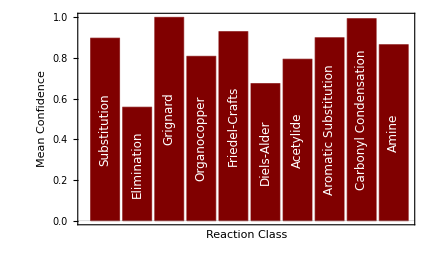

```mathematica
retConfBar=
BarChart[Map[Mean[#]&,Normal[Values@retDat[GroupBy[#"true rclass"&]][All,All,{"reaction number","conf"}][All,All,"conf"]]],ChartLabels->Placed[Style[#,White]&/@accClasses,Center,Rotate[#,90 Degree]&],ImageSize->6*72,FrameLabel->{"Reaction Class","Mean Confidence"},LabelStyle->{Black,12},ChartStyle->RGBColor["#800000"]]
```

```mathematica
Export["C:\\Users\\willr\\Desktop\\SchrierRsrch\\IBMRxn\\BorrelliPaper\\ret_confBar.pdf",retConfBar,ImageResolution->300];
```

### ΔCm & ΔSA

#### Bar Charts

```mathematica
BarChart[#[[2,1]],PlotLabel->#[[1]],ChartLabels->Placed[#[[2,2]],Below]]&/@Thread[{Normal[Keys@retDat[All,{"true rclass","retpred_deltaCM"}][GroupBy[#"true rclass"&]][All,All,"retpred_deltaCM"]],Thread[{Values[Normal[Values@retDat[All,{"true rclass","retpred_deltaCM","reaction number"}][GroupBy[#"true rclass"&]][All,All,{"retpred_deltaCM","reaction number"}]]][[All,All,1]],Values[Normal[Values@retDat[All,{"true rclass","retpred_deltaCM","reaction number"}][GroupBy[#"true rclass"&]][All,All,{"retpred_deltaCM","reaction number"}]]][[All,All,2]]}]}];
```

```mathematica
BarChart[#[[2,1]],PlotLabel->#[[1]],ChartLabels->Placed[#[[2,2]],Below]]&/@Thread[{Normal[Keys@retDat[All,{"true rclass","retpred_deltaSA"}][GroupBy[#"true rclass"&]][All,All,"retpred_deltaSA"]],Thread[{Values[Normal[Values@retDat[All,{"true rclass","retpred_deltaSA","reaction number"}][GroupBy[#"true rclass"&]][All,All,{"retpred_deltaSA","reaction number"}]]][[All,All,1]],Values[Normal[Values@retDat[All,{"true rclass","retpred_deltaSA","reaction number"}][GroupBy[#"true rclass"&]][All,All,{"retpred_deltaSA","reaction number"}]]][[All,All,2]]}]}];
```

#### Scatter Plots

```mathematica
(*true SA/Cm vs. Pred (tooltipped) *)
```

```mathematica
ListPlot[MapThread[Tooltip[#1,#2]&,{Normal[Values@retAllDat[All,{"true_deltaSA","retpred_deltaSA"}]],Normal[Values@retAllDat[All,{"reaction number","true rclass"}]]}],PlotLabel->"True vs. Pred ΔSA"];
```

```mathematica
retSAdat=Normal[Values@Values[retDat[All,{"reaction number","true rclass","true_deltaSA","retpred_deltaSA"}][GroupBy[#"true rclass"&]][[All,All,{"true_deltaSA","retpred_deltaSA"}]]]];
```

```mathematica
retCMdat=Normal[Values@Values[retDat[All,{"reaction number","true rclass","true_deltaCM","retpred_deltaCM"}][GroupBy[#"true rclass"&]][[All,All,{"true_deltaCM","retpred_deltaCM"}]]]];
```

```mathematica
retClasses={"Substitution","Elimination","Grignard","Friedel-Crafts","Aromatic Substitution","Diels-Alder","Amine","Carbonyl Condensation","Organocopper","Acetylide"};
```

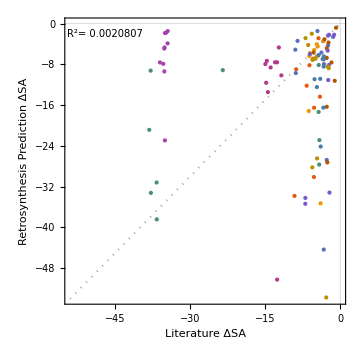
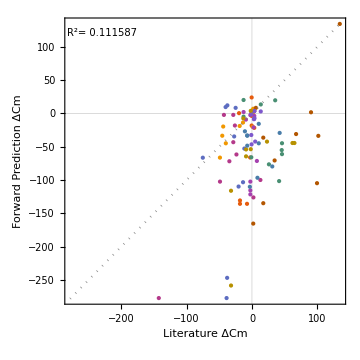

```mathematica
retSACM={Show[ListPlot[retSAdat,(*PlotLegends->retClasses,*)ImageSize->Medium,PlotRange->{{Floor[Min[{Min[Flatten[retSAdat,1][[All,1]]],Min[Flatten[retSAdat,1][[All,2]]]}]],Ceiling[Max[{Max[Flatten[retSAdat,1][[All,1]]],Max[Flatten[retSAdat,1][[All,2]]]}]]},{Floor[Min[{Min[Flatten[retSAdat,1][[All,1]]],Min[Flatten[retSAdat,1][[All,2]]]}]],Ceiling[Max[{Max[Flatten[retSAdat,1][[All,1]]],Max[Flatten[retSAdat,1][[All,2]]]}]]}},AspectRatio->1,LabelStyle->{Black,12},PlotStyle->PointSize[Medium]],

Plot[x,{x,Floor[Min[{Min[Flatten[retSAdat,1][[All,1]]],Min[Flatten[retSAdat,1][[All,2]]]}]],Ceiling[Max[{Max[Flatten[retSAdat,1][[All,1]]],Max[Flatten[retSAdat,1][[All,2]]]}]]},PlotStyle->{Gray,Dotted}],

Graphics[Text[Style["R^2= "<>ToString[Correlation[Flatten[retSAdat,1][[All,1]],Flatten[retSAdat,1][[All,2]]]^2],FontSize->10,Black],{-47,-2}]],FrameLabel->{"Literature ΔSA","Retrosynthesis Prediction ΔSA"}
],

Show[ListPlot[retCMdat,(*PlotLegends->retClasses,*)ImageSize->Medium,PlotRange->{{Floor[Min[{Min[Flatten[retCMdat,1][[All,1]]],Min[Flatten[retCMdat,1][[All,2]]]}]],Ceiling[Max[{Max[Flatten[retCMdat,1][[All,1]]],Max[Flatten[retCMdat,1][[All,2]]]}]]},{Floor[Min[{Min[Flatten[retCMdat,1][[All,1]]],Min[Flatten[retCMdat,1][[All,2]]]}]],Ceiling[Max[{Max[Flatten[retCMdat,1][[All,1]]],Max[Flatten[retCMdat,1][[All,2]]]}]]}},AspectRatio->1,LabelStyle->{Black,12},PlotStyle->PointSize[Medium]],

Plot[x,{x,Floor[Min[{Min[Flatten[retCMdat,1][[All,1]]],Min[Flatten[retCMdat,1][[All,2]]]}]],Ceiling[Max[{Max[Flatten[retCMdat,1][[All,1]]],Max[Flatten[retCMdat,1][[All,2]]]}]]},PlotStyle->{Gray,Dotted}],

Graphics[Text[Style["R^2= "<>ToString[Correlation[Flatten[retCMdat,1][[All,1]],Flatten[retCMdat,1][[All,2]]]^2],FontSize->10,Black],{-230,120}]],FrameLabel->{"Literature ΔCm","Forward Prediction ΔCm"}
]}
```

```mathematica
Export["C:\\Users\\willr\\Desktop\\SchrierRsrch\\Posters\\retSACM1.pdf",retSACM[[1]],"PDF",ImageResolution->1200];
```

## Low Confidence Reactions

### Substitution - 1 candidate

```mathematica
(* only reaction 10 is very low *)
```

```mathematica
subLC=SortBy[retDat[GroupBy[#"true rclass"&]][[1]],#conf&][[1]];
```

```mathematica
(* true and pred retro *)
```

```mathematica
MapThread[rxnPlt[#1,"",#2]&,{Normal[Values@subLC[{"true reaction smiles","pred reaction smiles"}]],{"true retro","pred retro"}}];
```

### Elimination - 5 candidates

```mathematica
(* take ones w/ conf < 0.5 *)
```

```mathematica
elimLC=SortBy[retDat[GroupBy[#"true rclass"&]][[2]],#conf&][[1;;5]];
```

```mathematica
(* true and pred retro *)
```

```mathematica
{rxnPlt[#[[1]],ToString[#[[3]]],"true retro"],rxnPlt[#[[2]],ToString[#[[3]]],"pred retro"]}&/@Normal[Values@elimLC[All,{"true reaction smiles","pred reaction smiles","reaction number"}]];
```

reaction 15: doesn’t seem to obey atom conservation
reaction 11: doesn’t seem to make sense
reaction 17: nonsensical, maybe no atom conservation (but stoichiometric) 
reaction 12: reduction of benzene with H_2 to cyclohexene (unlikely) 
reaction 20: reduction of benzene to the diene (likely)

```mathematica
rxnPlt[#,"",""]&/@Normal[retDat[Select[#"reaction number"==11&]][[1]][{"true reaction smiles","pred reaction smiles"}]];
```

### Grignard - 0 low confidence

```mathematica
grigLC=SortBy[combDatRet[GroupBy[#"true rclass"&]][[3]],#conf&];
```

Part::partw: Part 3 of combDatRet[GroupBy[#"true rclass"&]] does not exist.

Function::slot1: (#conf&)[combDatRet[GroupBy[#"true rclass"&]]] is expected to have an Association as the first argument.

Function::slot1: (#conf&)[3] is expected to have an Association as the first argument.

Part::pkspec1: The expression combDatRet[GroupBy[#"true rclass"&]] cannot be used as a part specification.

```mathematica
{rxnPlt[#[[1]],ToString[#[[3]]],"true retro"],rxnPlt[#[[2]],ToString[#[[3]]],"pred retro"]}&/@Normal[Values@grigLC[All,{"true reaction smiles","pred reaction smiles","reaction number"}]];
```

Values::invrl: The argument 3⟦combDatRet[GroupBy[#"true rclass"&]]⟧[All,{true reaction smiles,pred reaction smiles,reaction number}] is not a valid Association or a list of rules.

Part::partw: Part 3 of 3⟦combDatRet[GroupBy[#"true rclass"&]]⟧[All,{true reaction smiles,pred reaction smiles,reaction number}] does not exist.

Part::partw: Part 3 of 3⟦combDatRet[GroupBy[#"\"true rclass\""&]]⟧[All,{true reaction smiles,pred reaction smiles,reaction number}] does not exist.

Values::invrl: The argument {rxnPlt[All,3[[combDatRet[GroupBy[#"true rclass" & ]]]][All, {true reaction smiles, pred reaction smiles, reaction number}][[3]],true retro],rxnPlt[{true reaction smiles,pred reaction smiles,reaction number},3[[combDatRet[GroupBy[#"\"true rclass\"" & ]]]][All, {true reaction smiles, pred reaction smiles, reaction number}][[3]],pred retro]} is not a valid Association or a list of rules.

### Friedel Crafts - 2 candidates

```mathematica
(* take those less than 0.5 *)
```

```mathematica
fcLC=SortBy[retDat[GroupBy[#"true rclass"&]][[4]],#conf&][[1;;2]]
```

```mathematica
{rxnPlt[#[[1]],ToString[#[[3]]],"true retro"],rxnPlt[#[[2]],ToString[#[[3]]],"pred retro"]}&/@Normal[Values@fcLC[All,{"true reaction smiles","pred reaction smiles","reaction number"}]];
```

reaction 33: will probably work but starts with tosyl toluene to make toluene 
reaction 40: does an aromatic sub, meta to an activating o,p director

### Aromatic Substitution - 1 candidate

```mathematica
(* take those less than 0.5 *)
```

```mathematica
asubLC=SortBy[retDat[GroupBy[#"true rclass"&]][[5]],#conf&][[1]];
```

```mathematica
{rxnPlt[#[[1]],ToString[#[[3]]],"true retro"],rxnPlt[#[[2]],ToString[#[[3]]],"pred retro"]}&@Normal[Values@asubLC[{"true reaction smiles","pred reaction smiles","reaction number"}]]
```

{-Graphics-,-Graphics-}

reaction 42: probably work, very intense compared to acid catalyzed nitration

### Diels Alder - 4 candidates

```mathematica
daLC=SortBy[retDat[GroupBy[#"true rclass"&]][[6]],#conf&][[1;;4]];
```

```mathematica
{rxnPlt[#[[1]],ToString[#[[3]]],"true retro"],rxnPlt[#[[2]],ToString[#[[3]]],"pred retro"]}&/@Normal[Values@daLC[All,{"true reaction smiles","pred reaction smiles","reaction number"}]];
```

reaction 51: exactly correct, just low confidence
reaction 52: again, reduction of benzene to cyclohexene (unlikely) 
reaction 53: just oxidizes a carbonyl on the starting material (probably work fine) 
reaction 60: unsure, some reaction with Cl2 and SnCl4

### Amine - 2 (weak) candidates

```mathematica
aminLC=SortBy[retDat[GroupBy[#"true rclass"&]][[7]],#conf&][[1;;2]];
```

```mathematica
{rxnPlt[#[[1]],ToString[#[[3]]],"true retro"],rxnPlt[#[[2]],ToString[#[[3]]],"pred retro"]}&/@Normal[Values@aminLC[All,{"true reaction smiles","pred reaction smiles","reaction number"}]]
```

{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}

reaction 67: exactly correct, but low confidence
rxn 68: acid catalyzed ester hydrolysis (will work)

### Carbonyl Condensation - 1 candidate

```mathematica
condLC=SortBy[retDat[GroupBy[#"true rclass"&]][[8]],#conf&][[1]];
```

```mathematica
{rxnPlt[#[[1]],ToString[#[[3]]],"true retro"],rxnPlt[#[[2]],ToString[#[[3]]],"pred retro"]}&@Normal[Values@condLC[{"true reaction smiles","pred reaction smiles","reaction number"}]]
```

{-Graphics-,-Graphics-}

reaction 72: some kind of oxidation

### Organocopper - 0 low confidence

```mathematica
orgLC=SortBy[retDat[GroupBy[#"true rclass"&]][[9]],#conf&];
```

### Acetylide - 1 candidate

```mathematica
acetLC=SortBy[retDat[GroupBy[#"true rclass"&]][[10]],#conf&][[1]];
```

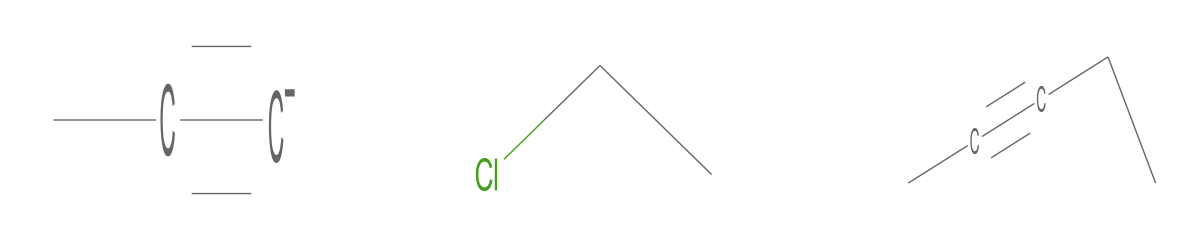
{-Graphics-,-Graphics-}

```mathematica
{rxnPlt[#[[1]],ToString[#[[3]]],"true retro"],rxnPlt[#[[2]],ToString[#[[3]]],"pred retro"]}&@Normal[Values@acetLC[{"true reaction smiles","pred reaction smiles","reaction number"}]]
```

reaction 92: atom conservation not observed

## Check All Reactions

```mathematica
Normal[DeleteDuplicates@retDat[All,"true rclass"]]
```

{substitution,elimination,grignard,friedelcrafts,asub,dielsalder,amine,carbonylcondensation,organocopper,acetylide}

### Substitution

```mathematica
subRets=retDat[Select[#"true rclass"=="substitution"&]];
```

```mathematica
{rxnPlt[#[[1]],ToString[#[[3]]],"true retro"],rxnPlt[#[[2]],ToString[#[[3]]],"pred retro"]}&/@Normal[Values@subRets[All,{"true reaction smiles","pred reaction smiles","reaction number"}]];
```

rxn 1: SN1 on primary alkyl halide (questionable) 
rxn 10: trying to add hydrogen over a carbonyl, and deuterium disappears?

### Elimination

```mathematica
elimRets=retDat[Select[#"true rclass"=="elimination"&]];
```

```mathematica
{rxnPlt[#[[1]],ToString[#[[3]]],"true retro"],rxnPlt[#[[2]],ToString[#[[3]]],"pred retro"]}&/@Normal[Values@elimRets[All,{"true reaction smiles","pred reaction smiles","reaction number"}]];
```

rxn 11: seems nonsensical
rxn 12: H_2 reduction of benzene to cyclohexene
rxn 15: grignard nuc. attack but # C’s not conserved
rxn 17: methane --> ethene (spontaneously?)
rxn 20: H_2 reduction of benzene to diene

### Grignard

```mathematica
grigRets=retDat[Select[#"true rclass"=="grignard"&]];
```

```mathematica
{rxnPlt[#[[1]],ToString[#[[3]]],"true retro"],rxnPlt[#[[2]],ToString[#[[3]]],"pred retro"]}&/@Normal[Values@grigRets[All,{"true reaction smiles","pred reaction smiles","reaction number"}]]
```

{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}

reaction 25: tries to cleave an ester linkage by H_2 and Pd reduction (similarly tried to do this over a carbonyl)

### Friedel Crafts

```mathematica
fcRets=retDat[Select[#"true rclass"=="friedelcrafts"&]];
```

```mathematica
{rxnPlt[#[[1]],ToString[#[[3]]],"true retro"],rxnPlt[#[[2]],ToString[#[[3]]],"pred retro"]}&/@Normal[Values@fcRets[All,{"true reaction smiles","pred reaction smiles","reaction number"}]];
```

reaction 31: interesting Weinreb synthesis 
reaction 33: p-toluenesulfonic acid + H_2 --> toluene (unsure about reducing the sulfonate group) (maybe another example of misplaced reduction) 
reaction 37: another weinreb synthesis
reaction 38: maybe wrong weinreb type synthesis

### Aromatic Substitution

```mathematica
asubRets=retDat[Select[#"true rclass"=="asub"&]];
```

```mathematica
{rxnPlt[#[[1]],ToString[#[[3]]],"true retro"],rxnPlt[#[[2]],ToString[#[[3]]],"pred retro"]}&/@Normal[Values@asubRets[All,{"true reaction smiles","pred reaction smiles","reaction number"}]]
```

{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}

reaction 41: trying diazonium salt coupling with HBr to add Br (usually done with CuBr) - rather than direct bromination
reaction 46: same interconversion as 41
reaction 47: same as 41 and 46 but with Cl, and uses CuCl so would probably work
reaction 49: same as 47

### Diels Alder

```mathematica
daRets=retDat[Select[#"true rclass"=="dielsalder"&]];
```

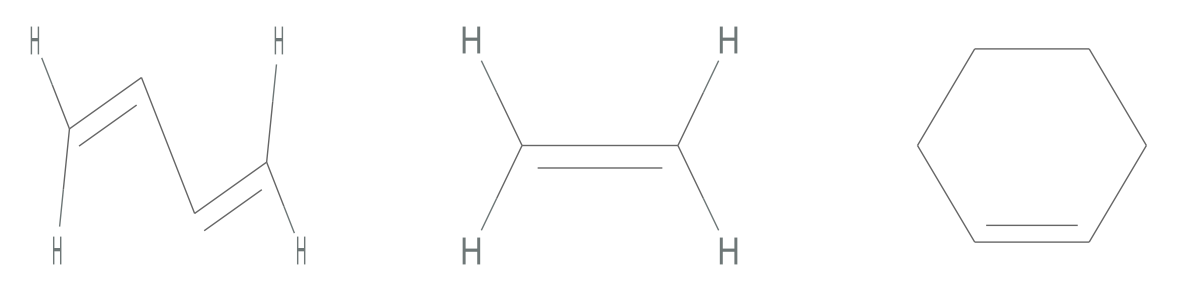
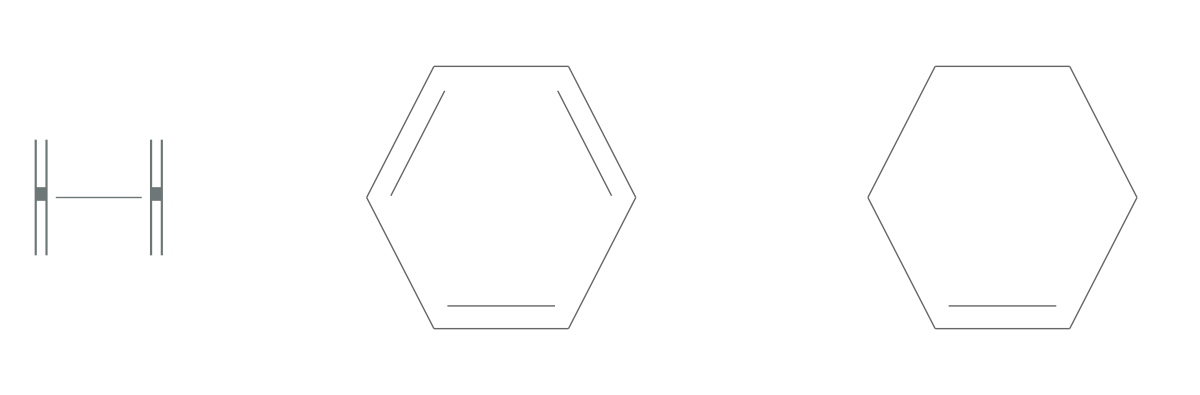
{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}

```mathematica
{rxnPlt[#[[1]],ToString[#[[3]]],"true retro"],rxnPlt[#[[2]],ToString[#[[3]]],"pred retro"]}&/@Normal[Values@daRets[All,{"true reaction smiles","pred reaction smiles","reaction number"}]]
```

reaction 56: carb acid --> ester, but random acid chloride involved
reaction 58: overly complex carb acid --> ester conversion

### Amine

```mathematica
aminRets=retDat[Select[#"true rclass"=="amine"&]];
```

```mathematica
{rxnPlt[#[[1]],ToString[#[[3]]],"true retro"],rxnPlt[#[[2]],ToString[#[[3]]],"pred retro"]}&/@Normal[Values@aminRets[All,{"true reaction smiles","pred reaction smiles","reaction number"}]]
```

{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}

### Carbonyl Condensation

```mathematica
condRets=retDat[Select[#"true rclass"=="carbonylcondensation"&]];
```

```mathematica
{rxnPlt[#[[1]],ToString[#[[3]]],"true retro"],rxnPlt[#[[2]],ToString[#[[3]]],"pred retro"]}&/@Normal[Values@condRets[All,{"true reaction smiles","pred reaction smiles","reaction number"}]]
```

{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}

reaction 71: very complex iodine-based coordination compound 
- favoring a lot of acetal hydrolyses

### Organocopper

```mathematica
orgRets=retDat[Select[#"true rclass"=="organocopper"&]];
```

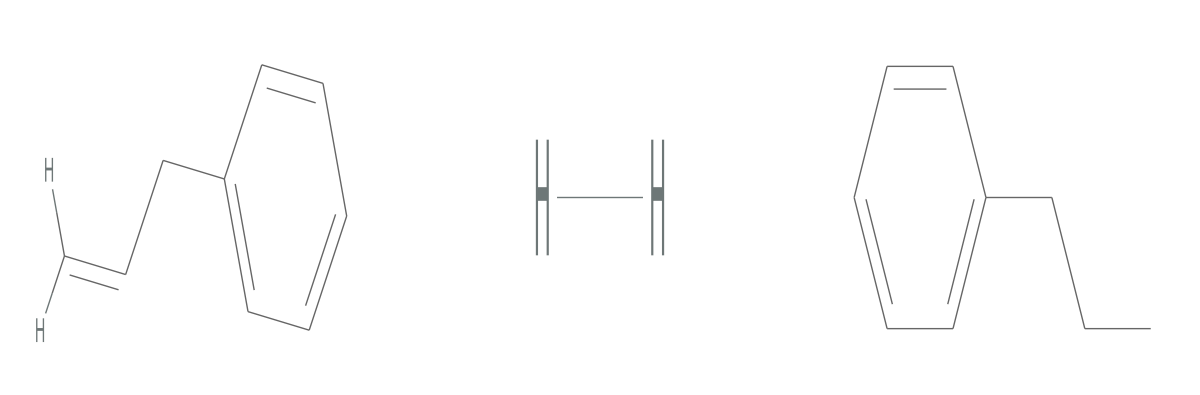
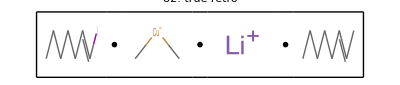
{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}

```mathematica
{rxnPlt[#[[1]],ToString[#[[3]]],"true retro"],rxnPlt[#[[2]],ToString[#[[3]]],"pred retro"]}&/@Normal[Values@orgRets[All,{"true reaction smiles","pred reaction smiles","reaction number"}]]
```

```mathematica
MoleculePlot@Molecule@#&/@Normal[retDat[Select[#"true rclass"=="organocopper"&]][All,"true prod"]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

### Acetylide

```mathematica
acetRets=retDat[Select[#"true rclass"=="acetylide"&]];
```

```mathematica
{rxnPlt[#[[1]],ToString[#[[3]]],"true retro"],rxnPlt[#[[2]],ToString[#[[3]]],"pred retro"]}&/@Normal[Values@acetRets[All,{"true reaction smiles","pred reaction smiles","reaction number"}]];
```

reaction 92: seems like # C’s are off
reaction 96: probably OK, but butylithium will deprotonate the alcohol too.

### High Confidence Rxn Analysis

```mathematica
retHCs=retDat[[{1,15,25,33,38,41,46,56,58,92}]];
```

```mathematica
retHCs=retHCs[Select[#conf>0.90&]];
```

```mathematica
Normal[{rxnPlt[#["pred reaction smiles"],"pred",ToString[#["reaction number"]]],rxnPlt[#["true reaction smiles"],"true",ToString[#["reaction number"]]]}&/@retHCs]
```

{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}

## Fwd Matches Retrosynthesis

```mathematica
fwdMatches=MapThread[Quiet[sameProd[#1,#2]]&,{Normal[retDat[All,"pred prod"]],Normal[retFwdDat[All,"pred prod"]]}];
```

```mathematica
fwdFMatches=Dataset[Flatten[Normal[{retDat[[#]],retFwdDat[[#]]}]]]&/@Position[fwdMatches,False];
```

```mathematica
(* all are when the forward reaction fails, so product is invalid *)
```

```mathematica
{MoleculePlot[Molecule#["pred prod"]]}&/@fwdFMatches[[1]];
```

```mathematica
Length@fwdFMatches
```

17

## Interesting Observations

### Substitution

#### Addition of H_2 Over Carbonyl

```mathematica
rxnPlt[#,"",""]&/@Normal[retDat[Select[#"reaction number"==10&]][[1]][{"true reaction smiles","pred reaction smiles"}]]
```

<|true reaction smiles→-Graphics-,pred reaction smiles→-Graphics-|>

```mathematica
retDat[Select[#"reaction number"==10&]][[1]]["true prod"]
```

```mathematica
IBMRxn["new project","test"]
```

Project Name | Project ID
test | 605e16d64fe89200014b1b16

```mathematica
test=IBMRxn["new retrosynthesis","605e16d64fe89200014b1b16",{"O[C@@]([H])([H])C"},"","dataset"];
```

```mathematica
rxnPlt[test[[1]]["rreac"]<>">>"<>test[[1]]["prod"],"",""]
```

-Graphics-

#### S_N 1 On Primary Alkyl Halide

```mathematica
rxnPlt[#,"",""]&/@Normal[retDat[Select[#"reaction number"==1&]][[1]][{"true reaction smiles","pred reaction smiles"}]]
```

<|true reaction smiles→-Graphics-,pred reaction smiles→-Graphics-|>

### Elimination

#### Potassium Tert-Butoxide Eliminating Itself

```mathematica
rxnPlt[#,"",""]&/@Normal[retDat[Select[#"reaction number"==11&]][[1]][{"true reaction smiles","pred reaction smiles","conf"}]]
```

<|true reaction smiles→-Graphics-,pred reaction smiles→-Graphics-,conf→rxnPlt[0.00182,,]|>

#### Grignard # C’s Inconsistent

```mathematica
rxnPlt[#,"",""]&/@Normal[retDat[Select[#"reaction number"==15&]][[1]][{"true reaction smiles","pred reaction smiles","conf"}]]
```

<|true reaction smiles→-Graphics-,pred reaction smiles→-Graphics-,conf→rxnPlt[0.0000196,,]|>

#### Methane → Ethene

```mathematica
rxnPlt[#,"",""]&/@Normal[retDat[Select[#"reaction number"==17&]][[1]][{"true reaction smiles","pred reaction smiles","conf"}]]
```

<|true reaction smiles→-Graphics-,pred reaction smiles→-Graphics-,conf→rxnPlt[0.0775,,]|>

### Grignard

#### Cleaving Ester w/ H_2

```mathematica
rxnPlt[#,"",""]&/@Normal[retDat[Select[#"reaction number"==25&]][[1]][{"true reaction smiles","pred reaction smiles","conf"}]]
```

<|true reaction smiles→-Graphics-,pred reaction smiles→-Graphics-,conf→rxnPlt[1.,,]|>

### Friedel Crafts

#### Weinreb Syntheses

```mathematica
rxnPlt[#,"",""]&/@Normal[retDat[Select[#"reaction number"==31&]][[1]][{"true reaction smiles","pred reaction smiles","conf"}]]
```

<|true reaction smiles→-Graphics-,pred reaction smiles→-Graphics-,conf→rxnPlt[1.,,]|>

```mathematica
rxnPlt[#,"",""]&/@Normal[retDat[Select[#"reaction number"==38&]][[1]][{"true reaction smiles","pred reaction smiles","conf"}]]
```

<|true reaction smiles→-Graphics-,pred reaction smiles→-Graphics-,conf→rxnPlt[1.,,]|>

#### Reducing Sulfonate Group w/ H_2

```mathematica
rxnPlt[#,"",""]&/@Normal[retDat[Select[#"reaction number"==33&]][[1]][{"true reaction smiles","pred reaction smiles","conf"}]]
```

<|true reaction smiles→-Graphics-,pred reaction smiles→-Graphics-,conf→rxnPlt[0.0114,,]|>

### ASub

#### Wrong Diazonium Salt Substitutions

```mathematica
rxnPlt[#,"",""]&/@Normal[retDat[Select[#"reaction number"==41&]][[1]][{"true reaction smiles","pred reaction smiles","conf"}]]
```

<|true reaction smiles→-Graphics-,pred reaction smiles→-Graphics-,conf→rxnPlt[1.,,]|>

```mathematica
rxnPlt[#,"",""]&/@Normal[retDat[Select[#"reaction number"==47&]][[1]][{"true reaction smiles","pred reaction smiles","conf"}]]
```

<|true reaction smiles→-Graphics-,pred reaction smiles→-Graphics-,conf→rxnPlt[1.,,]|>

### Friedel Crafts

#### Ester Synthesis w/ Random Acid Chloride

```mathematica
rxnPlt[#,"",""]&/@Normal[retDat[Select[#"reaction number"==56&]][[1]][{"true reaction smiles","pred reaction smiles","conf"}]]
```

<|true reaction smiles→-Graphics-,pred reaction smiles→-Graphics-,conf→rxnPlt[0.971,,]|>

### Carbonyl Condensation

#### Iodine Complex

```mathematica
rxnPlt[#,"",""]&/@Normal[retDat[Select[#"reaction number"==71&]][[1]][{"true reaction smiles","pred reaction smiles","conf"}]]
```

<|true reaction smiles→-Graphics-,pred reaction smiles→-Graphics-,conf→rxnPlt[0.97,,]|>

Favored many acetal hydrolyses.

### Acetylide

#### # of C’s Inconsistent

```mathematica
rxnPlt[#,"",""]&/@Normal[retDat[Select[#"reaction number"==92&]][[1]][{"true reaction smiles","pred reaction smiles","conf"}]]
```

<|true reaction smiles→-Graphics-,pred reaction smiles→-Graphics-,conf→rxnPlt[0.00648,,]|>

#### Butylithium w/ Alcohol Side Reaction

```mathematica
rxnPlt[#,"",""]&/@Normal[retDat[Select[#"reaction number"==96&]][[1]][{"true reaction smiles","pred reaction smiles","conf"}]]
```

<|true reaction smiles→-Graphics-,pred reaction smiles→-Graphics-,conf→rxnPlt[0.911,,]|>

## Synthesis

## Accuracy

```mathematica
synthDat//First//Keys//Normal
```

{reaction number,true rclass,true reaction smiles,true prod,pred reaction smiles,pred prod,conf,projID,predID,T1 Correct,T2 Correct,T3 Correct,T4 Correct,T5 Correct,true_deltaCM,true_deltaSA,fwdpredo_deltaCM,fwdpredo_deltaSA}

```mathematica
tnAcc[data_,class_,n_]:=Module[{reacs,reacAccs,correct},
reacs=data[Select[#"true rclass"==class&]];
reacAccs=reacs[All,{"T1 Correct","T2 Correct","T3 Correct","T4 Correct","T5 Correct"}];
correct=Select[Flatten[Normal[Values@reacAccs[[All,{n}]]]],#=="True"&];
(Length[correct]/Length[reacAccs])*100
]
```

```mathematica
{synthSubT1,synthElimT1,synthGrigT1,synthOrgT1,synthFCT1,synthDAT1,synthAcetT1,synthEsubT1,synthCondT1,synthAminT1}=tnAcc[synthDat,#,1]&/@DeleteDuplicates[Normal@synthDat[All,"true rclass"]];
```

```mathematica
{synthSubT2,synthElimT2,synthGrigT2,synthOrgT2,synthFCT2,synthDAT2,synthAcetT2,synthEsubT2,synthCondT2,synthAminT2}=tnAcc[synthDat,#,2]&/@DeleteDuplicates[Normal@synthDat[All,"true rclass"]];
```

```mathematica
{synthSubT3,synthElimT3,synthGrigT3,synthOrgT3,synthFCT3,synthDAT3,synthAcetT3,synthEsubT3,synthCondT3,synthAminT3}=tnAcc[synthDat,#,3]&/@DeleteDuplicates[Normal@synthDat[All,"true rclass"]];
```

```mathematica
{synthSubT4,synthElimT4,synthGrigT4,synthOrgT4,synthFCT4,synthDAT4,synthAcetT4,synthEsubT4,synthCondT4,synthAminT4}=tnAcc[synthDat,#,4]&/@DeleteDuplicates[Normal@synthDat[All,"true rclass"]];
```

```mathematica
{synthSubT5,synthElimT5,synthGrigT5,synthOrgT5,synthFCT5,synthDAT5,synthAcetT5,synthEsubT5,synthCondT5,synthAminT5}=tnAcc[synthDat,#,5]&/@DeleteDuplicates[Normal@synthDat[All,"true rclass"]];
```

```mathematica
Total[Map[(#/10)&,{synthSubT1,synthElimT1,synthGrigT1,synthOrgT1,synthFCT1,synthDAT1,synthAcetT1,synthEsubT1,synthCondT1,synthAminT1}]]
```

61

```mathematica
N[(Length[Select[Flatten[Normal[Values@Values[synthDat[GroupBy[#"true rclass"&]][[All,All,{"reaction number","true rclass","T1 Correct"}]]]][[All,All,-1]]],#=="True"&]]/1)]
```

61.

```mathematica
N[(Length[Select[Flatten[Normal[Values@Values[synthDat[GroupBy[#"true rclass"&]][[All,All,{"reaction number","true rclass","T2 Correct"}]]]][[All,All,-1]]],#=="True"&]]/100)]
```

0.69

```mathematica
N[(Length[Select[Flatten[Normal[Values@Values[synthDat[GroupBy[#"true rclass"&]][[All,All,{"reaction number","true rclass","T3 Correct"}]]]][[All,All,-1]]],#=="True"&]]/100)]
```

0.69

```mathematica
N[(Length[Select[Flatten[Normal[Values@Values[synthDat[GroupBy[#"true rclass"&]][[All,All,{"reaction number","true rclass","T4 Correct"}]]]][[All,All,-1]]],#=="True"&]]/100)]
```

0.69

```mathematica
N[(Length[Select[Flatten[Normal[Values@Values[synthDat[GroupBy[#"true rclass"&]][[All,All,{"reaction number","true rclass","T5 Correct"}]]]][[All,All,-1]]],#=="True"&]]/100)]
```

0.7

```mathematica
Quiet[{MoleculePlot[Molecule@#[[1]],PlotLabel->"True"],MoleculePlot[Molecule@#[[2]],PlotLabel->"Pred"]}&/@Normal[Values[synthDat[Select[#"T1 Correct"=="False"&]][All,{"true prod","pred prod"}]]]]
```

{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,MoleculePlot[Molecule[{""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""Br[Mg]c1ccccc1.CO""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""}[[2]]],PlotLabel→Pred]},{-Graphics-,MoleculePlot[Molecule[{""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""C=O.C[Mg]Br""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""}[[2]]],PlotLabel→Pred]},{-Graphics-,MoleculePlot[Molecule[{""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""CC(=O)Cl.CC[Mg]Cl""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""}[[2]]],PlotLabel→Pred]},{-Graphics-,MoleculePlot[Molecule[{""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""CCC[Mg]Br.COC(=O)c1ccccc1""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""}[[2]]],PlotLabel→Pred]},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,MoleculePlot[Molecule[{""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""CC(=O)Cl.CC(C)C[Cu-]CC(C)C.[Li+]""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""}[[2]]],PlotLabel→Pred]},{-Graphics-,MoleculePlot[Molecule[{""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""CC(=O)Cl.CCC[Cu-]CCC.[Li+]""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""}[[2]]],PlotLabel→Pred]},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,MoleculePlot[Molecule[{""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""O=C(Cl)CCC1CN(C(=O)c2ccccc2)c2ccccc21.[Al+3].[Cl-].[Cl-].[Cl-]""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""}[[2]]],PlotLabel→Pred]},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,MoleculePlot[Molecule[{""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""C=C.C=CC=C""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""}[[2]]],PlotLabel→Pred]},{-Graphics-,-Graphics-},{-Graphics-,MoleculePlot[Molecule[{""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""CCC(Cl)(Cl)C(C)(C)C.[NH2-].[Na+]""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""}[[2]]],PlotLabel→Pred]},{-Graphics-,MoleculePlot[Molecule[{""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""BrC(C1CCCCC1)C(Br)C1CCCCC1.[NH2-].[Na+]""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""}[[2]]],PlotLabel→Pred]},{-Graphics-,MoleculePlot[Molecule[{""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""C#CC.Cl""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""}[[2]]],PlotLabel→Pred]},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,MoleculePlot[Molecule[{""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""CC(=O)CCCC(C)=O.CC[O-]""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""}[[2]]],PlotLabel→Pred]},{-Graphics-,-Graphics-},{-Graphics-,MoleculePlot[Molecule[{""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""CCCBr.N""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""}[[2]]],PlotLabel→Pred]},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}

```mathematica
Quiet[MoleculeQ[Molecule[synthDat[[21]]["pred prod"]]]]
```

False

```mathematica
fwdFails=synthDat[Select[Not[MoleculeQ[Quiet[Molecule[#"pred prod"]]]]&]];
```

```mathematica
Length@fwdFails
```

13

```mathematica
fwdFails[GroupBy[#"true rclass"&]]
```

```mathematica
(* check out where the difference in atoms reacts -> prods is large *)
```

```mathematica
Clear[tallies]
```

```mathematica
atoms[reaction_String]:=Module[{tallies,prodAs,diffs},tallies={MoleculeValue[Molecule[StringSplit[reaction,">>"][[1]]],"ElementTally"],MoleculeValue[Molecule[StringSplit[reaction,">>"][[2]]],"ElementTally"]};
prodAs=tallies[[2]][[All,1]];
diffs=Table[First[Select[tallies[[2]],First[#]==prodAs[[i]]&]][[2]],{i,1,Length@prodAs}]-Table[First[Select[tallies[[1]],First[#]==prodAs[[i]]&]][[2]],{i,1,Length@prodAs}];
AssociationThread[prodAs,diffs]
]
```

```mathematica
PositionIndex[Quiet[atoms[Normal[synthDat[All,"pred reaction smiles"]]]]];
```

PositionIndex::invrp: The argument atoms[{CCCl.[OH-]>>CCO,CC(C)CBr.C[O-]>>COCC(C)C,BrCCC1CCCOC1.N>>NCCC1CCCOC1,CC(=O)[O-].CC(C)(C)Br>>CC(=O)OC(C)(C)C,C[C@H]1CC[C@@H](Br)CC1.[C-]#N>>C[C@H]1CC[C@H](C#N)CC1,CCC(N)CO.CCC(N)CO.ClCCCl>>CCC1COC(CC)N1,«40»,O=C(Cl)CCC(c1ccccc1)c1ccc(Cl)c(Cl)c1.[Al+3].[Cl-].[Cl-].[Cl-]>>O=C1CCC(c2ccc(Cl)c(Cl)c2)c2ccccc21,CCl.[Al+3].[Cl-].[Cl-].[Cl-].c1ccccc1>>ClCc1ccccc1,CCCC(=O)Cl.[Al+3].[Cl-].[Cl-].[Cl-].c1ccccc1>>CCCC(=O)c1ccccc1,CC(C)CCl.[Al+3].[Cl-].[Cl-].[Cl-].c1ccccc1>>CC(C)Cc1ccccc1,«50»}] is not a valid Association or a list.

```mathematica
Quiet[rxnPlt[#["pred reaction smiles"],"",ToString[#["reaction number"]]]&/@Normal[synthDat[[{6, 14, 17, 20, 26, 33, 35, 37, 39, 54, 70, 83, 84, 88}]][All,{"reaction number","pred reaction smiles"}]]];
```

```mathematica
accDifs[orig_,s1_,s2_]:=N[((s2-orig)+(s1-orig))/2]
```

```mathematica
accDifs[70,96,85]
```

20.5

## Distribution Based Analysis

### Accuracy

```mathematica
accClasses={"Substitution","Elimination","Grignard","Organocopper","Friedel-Crafts","Diels-Alder","Acetylide","Aromatic Substitution","Carbonyl Condensation","Amine"};
```

```mathematica
accs=Values[Table[(((#["True"]/(#["True"]+#["False"])))*100)&/@Map[Counts[#]&,Normal[synthDat[GroupBy[#"true rclass"&]][[All,All,-9;;-5]][[All,All,i]]]],{i,1,5}]];
```

```mathematica
StringRiffle[SetPrecision[#,3]&/@accs[[All,10]]," & "]
```

60.0 & 60.0 & 60.0 & 60.0 & 60.0

```mathematica
topkAccs=ListLinePlot[{accs[[All,1]],accs[[All,2]],accs[[All,3]],accs[[All,4]],accs[[All,5]],accs[[All,6]],accs[[All,7]],accs[[All,8]],accs[[All,9]],accs[[All,10]]},PlotMarkers->Automatic,PlotLegends->accClasses,FrameLabel->{"Top-K Prediction","Accuracy (%)"},PlotRange->{{0.9,5.1},{0,100}},PlotLabel->"Top-K Accuracies",ImageSize->7*72,FrameTicks->{{Range[0,100,10],None},{Range[1,5],None}},LabelStyle->{Black,12}]
```

-Graphics-

```mathematica
Export["C:\\Users\\willr\\Desktop\\SchrierRsrch\\IBMRxn\\BorrelliPaper\\synth_topkAccsPlt.pdf",topkAccs,ImageResolution->300];
```

### Confidence

```mathematica
(* distribution of confidence scores bar charts *)
```

```mathematica
BarChart[#[[2,1]],PlotLabel->#[[1]],ChartLabels->Placed[#[[2,2]],Below]]&/@Thread[{Normal[Keys@synthDat[All,{"true rclass","conf"}][GroupBy[#"true rclass"&]][All,All,"conf"]],Thread[{Values[Normal[Values@synthDat[All,{"true rclass","conf","reaction number"}][GroupBy[#"true rclass"&]][All,All,{"conf","reaction number"}]]][[All,All,1]],Values[Normal[Values@synthDat[All,{"true rclass","conf","reaction number"}][GroupBy[#"true rclass"&]][All,All,{"conf","reaction number"}]]][[All,All,2]]}]}];
```

```mathematica
(* bar chart of mean confidence values *)
```

```mathematica
synthConfBar=BarChart[Map[Mean[#]&,Normal[Values@synthDat[GroupBy[#"true rclass"&]][All,All,{"reaction number","conf"}][All,All,"conf"]]],ChartLabels->Placed[Style[#,White]&/@accClasses,Center,Rotate[#,90 Degree]&],ImageSize->6*72,FrameLabel->{"Reaction Class","Mean Confidence"},LabelStyle->{Black,12},ChartStyle->RGBColor["#800000"]]
```

-Graphics-

```mathematica
Export["C:\\Users\\willr\\Desktop\\SchrierRsrch\\IBMRxn\\BorrelliPaper\\synth_confBar.pdf",synthConfBar,ImageResolution->300];
```

```mathematica
(* bar chart of mean confidence values and rescaled accuracies
```

```mathematica
BarChart[Thread[{Map[Mean[#]&,Normal[Values@synthDat[GroupBy[#"true rclass"&]][All,All,{"reaction number","conf"}][All,All,"conf"]]],Rescale[accs[[1]]]}]]
```

-Graphics-

### SA & Cm

```mathematica
synthDat//First//Keys//Normal
```

{reaction number,true rclass,true reaction smiles,true prod,pred reaction smiles,pred prod,conf,projID,predID,T1 Correct,T2 Correct,T3 Correct,T4 Correct,T5 Correct,true_deltaCM,true_deltaSA,fwdpredo_deltaCM,fwdpredo_deltaSA}

```mathematica
synthSAdat=Normal[Values@Values[synthDat[All,{"reaction number","true rclass","true_deltaSA","fwdpredo_deltaSA"}][GroupBy[#"true rclass"&]][[All,All,{"true_deltaSA","fwdpredo_deltaSA"}]]]];
```

```mathematica
synthCMdat=Normal[Values@Values[synthDat[All,{"reaction number","true rclass","true_deltaCM","fwdpredo_deltaCM"}][GroupBy[#"true rclass"&]][[All,All,{"true_deltaCM","fwdpredo_deltaCM"}]]]];
```

```mathematica
synthClasses=Normal[Keys[synthDat[All,{"reaction number","true rclass","true_deltaSA","fwdpredo_deltaSA"}][GroupBy[#"true rclass"&]]]]
```

{substitution,elimination,grignard,organocopper,friedelcrafts,dielsalder,acetylide,asub,carbonylcondensation,amine}

```mathematica
synthClasses={"Substitution","Elimination","Grignard","Organocopper","Friedel-Crafts","Diels-Alder","Acetylide","Aromatic Substitution","Carbonyl Condensation","Amine"};
```

```mathematica
colors=(("DefaultPlotStyle"/.(Method/.Charting`ResolvePlotTheme["Scientific",ListLinePlot]))/.Directive[x_,__]:>x)
```

{RGBColor[0.9, 0.36, 0.054],RGBColor[0.365248, 0.427802, 0.758297],RGBColor[0.945109, 0.593901, 0.],RGBColor[0.645957, 0.253192, 0.685109],RGBColor[0.285821, 0.56, 0.450773],RGBColor[0.7, 0.336, 0.],RGBColor[0.491486, 0.345109, 0.8],RGBColor[0.71788, 0.568653, 0.],RGBColor[0.70743, 0.224, 0.542415],RGBColor[0.287228, 0.490217, 0.664674],RGBColor[0.982289285128704, 0.5771321368979874, 0.011542503255145636],RGBColor[0.5876740325800278, 0.2877284499870081, 0.7500695697462922],RGBColor[0.4262088601796793, 0.5581552810007578, 0.2777996730417023],RGBColor[0.9431487543762861, 0.414555896337833, 0.07140829055870854],RGBColor[0.41497437140121635, 0.393632147507352, 0.7842993779115092]}

```mathematica
Placed[LineLegend[{Style["ξ = 10",Bold,14],Style["ξ = 50",Bold,14],Style["ξ = 100",Bold,14]},LegendFunction->Frame,LegendLayout->"Row"],{Center,Top}]
```

```mathematica
synthSACM={Show[ListPlot[synthSAdat,(*PlotLegends->synthClasses,*)ImageSize->5*72,PlotRange->{{Floor[Min[{Min[Flatten[synthSAdat,1][[All,1]]],Min[Flatten[synthSAdat,1][[All,2]]]}]],Ceiling[Max[{Max[Flatten[synthSAdat,1][[All,1]]],Max[Flatten[synthSAdat,1][[All,2]]]}]]},{Floor[Min[{Min[Flatten[synthSAdat,1][[All,1]]],Min[Flatten[synthSAdat,1][[All,2]]]}]],Ceiling[Max[{Max[Flatten[synthSAdat,1][[All,1]]],Max[Flatten[synthSAdat,1][[All,2]]]}]]}},AspectRatio->1,LabelStyle->{Black,12},PlotStyle->PointSize[Medium](*,PlotLegends->Placed[Framed[PointLegend[colors,synthClasses,LegendMargins->0]],{-30,-5}]*)],

Plot[x,{x,Floor[Min[{Min[Flatten[synthSAdat,1][[All,1]]],Min[Flatten[synthSAdat,1][[All,2]]]}]],Ceiling[Max[{Max[Flatten[synthSAdat,1][[All,1]]],Max[Flatten[synthSAdat,1][[All,2]]]}]]},PlotStyle->{Gray,Dotted}],

Graphics[Text[Style["R^2= "<>ToString[Correlation[Flatten[synthSAdat,1][[All,1]],Flatten[synthSAdat,1][[All,2]]]^2],FontSize->10,Black],{-4,-37.5}]],FrameLabel->{"Literature ΔSA","Forward Prediction ΔSA"}
],

Show[ListPlot[synthCMdat,(*PlotLegends->synthClasses,*)ImageSize->5*72,PlotRange->{{Floor[Min[{Min[Flatten[synthCMdat,1][[All,1]]],Min[Flatten[synthCMdat,1][[All,2]]]}]],Ceiling[Max[{Max[Flatten[synthCMdat,1][[All,1]]],Max[Flatten[synthCMdat,1][[All,2]]]}]]},{Floor[Min[{Min[Flatten[synthCMdat,1][[All,1]]],Min[Flatten[synthCMdat,1][[All,2]]]}]],Ceiling[Max[{Max[Flatten[synthCMdat,1][[All,1]]],Max[Flatten[synthCMdat,1][[All,2]]]}]]}},AspectRatio->1,LabelStyle->{Black,12},PlotStyle->PointSize[Medium]],

Plot[x,{x,Floor[Min[{Min[Flatten[synthCMdat,1][[All,1]]],Min[Flatten[synthCMdat,1][[All,2]]]}]],Ceiling[Max[{Max[Flatten[synthCMdat,1][[All,1]]],Max[Flatten[synthCMdat,1][[All,2]]]}]]},PlotStyle->{Gray,Dotted}],

Graphics[Text[Style["R^2= "<>ToString[Correlation[Flatten[synthCMdat,1][[All,1]],Flatten[synthCMdat,1][[All,2]]]^2],FontSize->10,Black],{150,-70}]],FrameLabel->{"Literature ΔCm","Forward Prediction ΔCm"}
]}
```

{-Graphics-,-Graphics-}

### Tao

```mathematica
taosInd=Table[AssociationThread[Normal[DeleteDuplicates@synthDat[All,"true rclass"]]->(tao[synthAllDat,#,i,"individual"]&/@Normal[DeleteDuplicates@synthAllDat[All,"true rclass"]])]//Dataset//ReverseSort,{i,1,5}];
```

```mathematica
taosGrp=Table[AssociationThread[Normal[DeleteDuplicates@synthDat[All,"true rclass"]]->(tao[synthAllDat,#,i,"group"]&/@Normal[DeleteDuplicates@synthAllDat[All,"true rclass"]])]//Dataset//ReverseSort,{i,1,5}];
```

```mathematica
Keys@taos[[1]]//Normal
```

Part::partd: Part specification taos⟦1⟧ is longer than depth of object.

Keys::invrl: The argument taos⟦1⟧ is not a valid Association or a list of rules.

Keys[taos⟦1⟧]

```mathematica
taoClasses={"Substitution","Diels-Alder","Acetylide","Aromatic Substitution","Amine","Carbonyl Condensation","Organocopper","Friedel-Crafts","Grignard","Elimination"};
```

```mathematica
tao=ListLinePlot[{Map[#["substitution"]&,taosInd],Map[#["dielsalder"]&,taosInd],Map[#["acetylide"]&,taosInd],Map[#["asub"]&,taosInd],Map[#["amine"]&,taosInd],Map[#["carbonylcondensation"]&,taosInd],Map[#["organocopper"]&,taosInd],Map[#["friedelcrafts"]&,taosInd],Map[#["grignard"]&,taosInd],Map[#["elimination"]&,taosInd]},PlotMarkers->Automatic,PlotLegends->taoClasses,ImageSize->7*72,PlotRange->{{0.9,5.1},{-600,20}},LabelStyle->{Black,12},FrameLabel->{"Top-K Prediction","Cumulative Tao Score"},PlotLabel->"Cumulative Tao Scores"]
```

-Graphics-

```mathematica
Export["C:\\Users\\willr\\Desktop\\SchrierRsrch\\IBMRxn\\BorrelliPaper\\synth_topkTaosPlt.pdf",tao,ImageResolution->300];
```

```mathematica
ListLinePlot[{Map[#["substitution"]&,taosGrp],Map[#["dielsalder"]&,taosGrp],Map[#["acetylide"]&,taosGrp],Map[#["asub"]&,taosGrp],Map[#["amine"]&,taosGrp],Map[#["carbonylcondensation"]&,taosGrp],Map[#["organocopper"]&,taosGrp],Map[#["friedelcrafts"]&,taosGrp],Map[#["grignard"]&,taosGrp],Map[#["elimination"]&,taosGrp]},PlotMarkers->Automatic,PlotLegends->taoClasses,ImageSize->7*72,PlotRange->{{0.9,5.1},{-1500,20}}]
```

-Graphics-

## Low Confidence

```mathematica
DeleteDuplicates[Normal@synthDat[All,"true rclass"]]
```

{substitution,elimination,grignard,organocopper,friedelcrafts,dielsalder,acetylide,asub,carbonylcondensation,amine}

### Substitution - few weak candidates

```mathematica
fwdSubLC=Sort[SortBy[synthDat[GroupBy[#"true rclass"&]][[1]],#conf&][Select[#conf<0.5&]]];
```

```mathematica
{rxnPlt[#[[1]],ToString[#[[3]]],"true rxn"],rxnPlt[#[[2]],ToString[#[[3]]],"pred rxn"]}&/@Normal[Values@fwdSubLC[All,{"true reaction smiles","pred reaction smiles","reaction number"}]]
```

{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}

### Elimination - 1 candidate

```mathematica
fwdElimLC=Sort[SortBy[synthDat[GroupBy[#"true rclass"&]][[2]],#conf&][Select[#conf<0.5&]]];
```

```mathematica
{rxnPlt[#[[1]],ToString[#[[3]]],"true rxn"],rxnPlt[#[[2]],ToString[#[[3]]],"pred rxn"]}&/@Normal[Values@fwdElimLC[All,{"true reaction smiles","pred reaction smiles","reaction number"}]]
```

{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}

reaction 13: predicts breaking a benzylic C-C bond

```mathematica
rxnPlt[#,"",""]&/@Normal[synthDat[Select[#"reaction number"==13&]][[1]][{"true reaction smiles","pred reaction smiles"}]]
```

<|true reaction smiles→-Graphics-,pred reaction smiles→-Graphics-|>

### Grignard - 0 candidates

```mathematica
fwdGrigLC=Sort[SortBy[synthDat[GroupBy[#"true rclass"&]][[3]],#conf&][Select[#conf<0.5&]]]
```

```mathematica
{rxnPlt[#[[1]],ToString[#[[3]]],"true rxn"],rxnPlt[#[[2]],ToString[#[[3]]],"pred rxn"]}&/@Normal[Values@fwdGrigLC[All,{"true reaction smiles","pred reaction smiles","reaction number"}]]
```

{}

### Organocopper - 3 candidates, 2 failures

```mathematica
fwdOrgLC=Sort[SortBy[synthDat[GroupBy[#"true rclass"&]][[4]],#conf&][Select[#conf<0.5&]]];
```

```mathematica
Quiet[{rxnPlt[#[[1]],ToString[#[[3]]],"true rxn"],rxnPlt[#[[2]],ToString[#[[3]]],"pred rxn"]}&/@Normal[Values@fwdOrgLC[All,{"true reaction smiles","pred reaction smiles","reaction number"}]]]
```

{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}

reaction 36: failure
reaction 38: failure
reaction 39: not matching # of C’s in Gilman reagent

```mathematica
rxnPlt[#,"",""]&/@Normal[synthDat[Select[#"reaction number"==39&]][[1]][{"true reaction smiles","pred reaction smiles"}]]
```

<|true reaction smiles→-Graphics-,pred reaction smiles→-Graphics-|>

### Friedel Crafts - 1 failure

```mathematica
fwdFCLC=Sort[SortBy[synthDat[GroupBy[#"true rclass"&]][[5]],#conf&][Select[#conf<0.5&]]];
```

```mathematica
{rxnPlt[#[[1]],ToString[#[[3]]],"true rxn"],rxnPlt[#[[2]],ToString[#[[3]]],"pred rxn"]}&/@Normal[Values@fwdFCLC[All,{"true reaction smiles","pred reaction smiles","reaction number"}]]
```

Molecule::nintrp: Unable to interpret {""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""…""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""O=C(Cl)CCC1CN(C(=O)c2ccccc2)c2ccccc21 as a name or chemical identifier.

MoleculePlot::mol: Argument Molecule[{"""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""…"""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""""O=C(Cl)CCC1CN(C(=O)c2ccccc2)c2ccccc21] is not a valid molecule.

Molecule::nintrp: Unable to interpret … as a name or chemical identifier.

MoleculePlot::mol: Argument … is not a valid molecule.

{{-Graphics-,-Graphics-}}

reaction 46: failure

### Diels Alder - 1 candidate

```mathematica
fwdDALC=Sort[SortBy[synthDat[GroupBy[#"true rclass"&]][[6]],#conf&][Select[#conf<0.5&]]];
```

```mathematica
{rxnPlt[#[[1]],ToString[#[[3]]],"true rxn"],rxnPlt[#[[2]],ToString[#[[3]]],"pred rxn"]}&/@Normal[Values@fwdDALC[All,{"true reaction smiles","pred reaction smiles","reaction number"}]]
```

{{-Graphics-,-Graphics-}}

reaction 54: favors forming a 4 membered ring

### Acetylide - 2 failures (double elim)

```mathematica
fwdAcetLC=Sort[SortBy[synthDat[GroupBy[#"true rclass"&]][[7]],#conf&][Select[#conf<0.5&]]];
```

```mathematica
{rxnPlt[#[[1]],ToString[#[[3]]],"true rxn"],rxnPlt[#[[2]],ToString[#[[3]]],"pred rxn"]}&/@Normal[Values@fwdAcetLC[All,{"true reaction smiles","pred reaction smiles","reaction number"}]]
```

Molecule::nintrp: Unable to interpret … as a name or chemical identifier.

MoleculePlot::mol: Argument … is not a valid molecule.

Molecule::nintrp: Unable to interpret … as a name or chemical identifier.

MoleculePlot::mol: Argument … is not a valid molecule.

Molecule::nintrp: Unable to interpret … as a name or chemical identifier.

General::stop: Further output of Molecule::nintrp will be suppressed during this calculation.

MoleculePlot::mol: Argument … is not a valid molecule.

General::stop: Further output of MoleculePlot::mol will be suppressed during this calculation.

{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}

reaction 68: failure (double elimination example)
reaction 69: failure (double elimination example)

### ESub - 0 candidates

```mathematica
fwdEsubLC=Sort[SortBy[synthDat[GroupBy[#"true rclass"&]][[8]],#conf&][Select[#conf<0.5&]]]
```

```mathematica
{rxnPlt[#[[1]],ToString[#[[3]]],"true rxn"],rxnPlt[#[[2]],ToString[#[[3]]],"pred rxn"]}&/@Normal[Values@fwdGrigLC[All,{"true reaction smiles","pred reaction smiles","reaction number"}]]
```

{}

### Carbonyl Condensation

```mathematica
fwdCondLC=Sort[SortBy[synthDat[GroupBy[#"true rclass"&]][[9]],#conf&][Select[#conf<0.5&]]];
```

```mathematica
{rxnPlt[#[[1]],ToString[#[[3]]],"true rxn"],rxnPlt[#[[2]],ToString[#[[3]]],"pred rxn"]}&/@Normal[Values@fwdCondLC[All,{"true reaction smiles","pred reaction smiles","reaction number"}]]
```

{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}

### Amine - 1 candidate (no rxn)

```mathematica
fwdAminLC=Sort[SortBy[synthDat[GroupBy[#"true rclass"&]][[10]],#conf&][Select[#conf<0.5&]]];
```

```mathematica
{rxnPlt[#[[1]],ToString[#[[3]]],"true rxn"],rxnPlt[#[[2]],ToString[#[[3]]],"pred rxn"]}&/@Normal[Values@fwdAminLC[All,{"true reaction smiles","pred reaction smiles","reaction number"}]]
```

{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}

reaction 94: no reaction

### General Low Confidence Analysis

```mathematica
synthLCs=Join[fwdSubLC,fwdElimLC,fwdGrigLC,fwdOrgLC,fwdFCLC,fwdDALC,fwdAcetLC,fwdEsubLC,fwdCondLC,fwdAminLC];
```

```mathematica
synthLCs//First//Keys//Normal
```

{reaction number,true rclass,true reaction smiles,true prod,pred reaction smiles,pred prod,conf,projID,predID,T1 Correct,T2 Correct,T3 Correct,T4 Correct,T5 Correct,true_deltaCM,true_deltaSA,fwdpredo_deltaCM,fwdpredo_deltaSA}

```mathematica
Select[Normal[synthLCs[All,"T1 Correct"]],#=="True"&]
```

{True,True,True,True,True,True,True,True}

## Check All Reactions

```mathematica
synthConfFails=ReverseSortBy[synthDat[Select[#"T1 Correct"=="False"&]],#conf&][Select[#conf>0.9&]];
```

```mathematica
Length@synthConfFails
```

12

```mathematica
(* how many failed *)
```

```mathematica
Length@synthConfFails[Select[Quiet[Not[MoleculeQ[Molecule[#"pred prod"]]]]&]]
```

2

```mathematica
synthConfFails//First//Keys//Normal
```

{reaction number,true rclass,true reaction smiles,true prod,pred reaction smiles,pred prod,conf,projID,predID,T1 Correct,T2 Correct,T3 Correct,T4 Correct,T5 Correct,true_deltaCM,true_deltaSA,fwdpredo_deltaCM,fwdpredo_deltaSA}

```mathematica
Normal[{Quiet[Normal[rxnPlt[Normal[#["pred reaction smiles"]],"pred",ToString[Normal[#["reaction number"]]]]]],Quiet[Normal[rxnPlt[Normal[#["true reaction smiles"]],"true",ToString[Normal[#["reaction number"]]]]]]}&/@synthConfFails]
```

{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}

```mathematica
Normal[{Quiet[Normal[rxnPlt[Normal[#["pred reaction smiles"]],"pred",ToString[Normal[#["reaction number"]]]]]],Quiet[Normal[rxnPlt[Normal[#["true reaction smiles"]],"true",ToString[Normal[#["reaction number"]]]]]]}&/@synthConfFails[Select[#"true rclass"=="elimination"&]]]
```

{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}

```mathematica
Length@synthConfFails[Select[#"true rclass"=="elimination"&]]
```

6

```mathematica
Molecule["ethanol"]["CanonicalSMILES"]
```

CCO

```mathematica
rxnPlt[synthDat[Select[#"true prod"=="CCO"&]][[1]]["true reaction smiles"],"",""]
```

-Graphics-

## Interesting Observations

```mathematica
(*IBMRxn["new project","intObs"]
```

```mathematica
ioProjID="603d377071c8b60001401f09";
```

### Equivalents

```mathematica
(* want a double elimination of the two bromines to make an alkyne, but it predicts single elimination *)
```

```mathematica
synthDat[Select[#"true rclass"=="elimination"&]][[-1]]
```

```mathematica
{rxnPlt[synthDat[Select[#"true rclass"=="elimination"&]][[-1]]["true reaction smiles"],"true",""],rxnPlt[synthDat[Select[#"true rclass"=="elimination"&]][[-1]]["pred reaction smiles"],"pred",""]}
```

{-Graphics-,-Graphics-}

```mathematica
(* providing two equivalents of base is a problem *)
```

```mathematica
twoEqs=IBMRxn["new prediction",{"CC(C)(C(Br)CBr)C","[O-]C(C)(C)C","[O-]C(C)(C)C"},ioProjID,"dataset"];
```

ResourceObject::updav: There is an update available for resource "SVGImport". Use ResourceUpdate[SVGImport] to get the update.

```mathematica
twoEqs
```

```mathematica
twoEqs["reaction image"]
```

-Graphics-

```mathematica
(* what about reacting the single-eliminated product again, with another eq of base? *)
```

```mathematica
synthDat[Select[#"true rclass"=="elimination"&]][[-1]]["pred reaction smiles"]
```

CC(C)(C)C(Br)CBr.CC(C)(C)[O-]>>C=C(Br)C(C)(C)C

```mathematica
reac2=IBMRxn["new prediction",{"C=C(Br)C(C)(C)C","[O-]C(C)(C)C"},ioProjID,"dataset"];
```

StringJoin::string: String expected at position 2 in rxn.res.ibm.com/rxn/api/api/v1/predictions/<><|payload→Null,metadata→<|uiMessages→<|errors→{},infos→{},warnings→{}|>,extendedPagination→<||>|>|>[payload,id].

StringReplace::strse: String or list of strings expected at position 1 in StringReplace[payload[name],_~~___→].

ResourceObject::updav: There is an update available for resource "ResourceFunctionMessage". Use ResourceUpdate[ResourceFunctionMessage] to get the update.

ResourceObject::updav: There is an update available for resource "BlockProtected". Use ResourceUpdate[BlockProtected] to get the update.

ResourceFunction::usermessage: SVGImport

Part::partw: Part 2 of reacSplit[payload[smiles]] does not exist.

```mathematica
reac2
```

```mathematica
reac2["reaction image"]
```

[◼] | SVGImport [payload[reactionImage]]

### Nucleophile Differences

```mathematica
nucOH=IBMRxn["new prediction",{"CCCCl","[OH-]"},ioProjID,"dataset"];
```

```mathematica
Pause[60];
```

```mathematica
nucSH=IBMRxn["new prediction",{"CCCCl","[SH-]"},ioProjID,"dataset"];
```

ResourceFunction::usermessage: SVGImport

```mathematica
{{nucOH["reaction image"],"conf"->nucOH["conf"]},{nucSH["reaction image"],,"conf"->nucSH["conf"]}}
```

{{-Graphics-,conf→0.7915},{[◼] | SVGImport [Null],Null,conf→0.848547}}

## Mixed Figures

### SA and Cm

```mathematica
GraphicsGrid[{synthSACM,retSACM},ImageSize->15*72];
```

```mathematica
sacm=(*Legended[*)Grid[{synthSACM,retSACM}](*,Framed[PointLegend[colors,synthClasses]]]*)
```

-Graphics- | -Graphics-
-Graphics- | -Graphics-

```mathematica
Framed[PointLegend[colors,synthClasses,LabelStyle->10]]
```

```mathematica
sacm=Overlay[{GraphicsGrid[{synthSACM,retSACM},ImageSize->12*72],Framed[PointLegend[colors,synthClasses,LabelStyle->8]]},Alignment->{-0.85,0.9}]
```

-Graphics-

```mathematica
Export["C:\\Users\\willr\\Desktop\\SchrierRsrch\\IBMRxn\\BorrelliPaper\\sacmPlt.pdf",sacm,ImageResolution->300];
```

### Confidence

```mathematica
classes=Normal[Keys[synthDat[GroupBy[#"true rclass"&]]]];
```

```mathematica
GraphicsGrid[Partition[MapThread[BarChart[#1,PlotLabel->#2,ChartLegends->{"Fwd Pred","Ret Pred"},ImageSize->5*72]&,{MapThread[Thread[{#1,#2}]&,{Table[Normal[synthDat[Select[#"true rclass"==ToString[i]&]][All,"conf"]],{i,classes}],Table[Normal[retDat[Select[#"true rclass"==ToString[i]&]][All,"conf"]],{i,classes}]}],classes}],5],ImageSize->20*72,Spacings->Scaled[0.5]]
```

-Graphics-

```mathematica
GraphicsGrid[Partition[MapThread[BarChart[#1,PlotLabel->#2,ChartLegends->{"Fwd Pred","Ret Pred"},ImageSize->5*72]&,{MapThread[Thread[{#1,#2}]&,{Table[Normal[synthDat[Select[#"true rclass"==ToString[i]&]][All,"conf"]],{i,classes[[1;;4]]}],Table[Normal[retDat[Select[#"true rclass"==ToString[i]&]][All,"conf"]],{i,classes[[1;;4]]}]}],classes[[1;;4]]}],2],AspectRatio->Full,ImageSize->{12*72,7*72}];
```

## Reaction Map

```mathematica
(* reaction map confidence distribution for all correct T1 predictions *)
```

```mathematica
Histogram[sT1CmapDat,FrameLabel->{"Reaction Map Confidence","Counts"}]
```

-Graphics-

```mathematica
(* reaction map confidence distribution for incorrect T1 predictions *)
```

```mathematica
Histogram[sT1WRmapDat,FrameLabel->{"Reaction Map Confidence","Counts"}]
```

-Graphics-